```mathematica
(*HELMHOLTZ COLLOCATION - 10 NODE TRIANGLES*)

Helmholtz Equation (General From):

In this program we will develop the Collocation version of the eigenvalue method, utilizing the Helmholtz equation.   The equation may be used to model standing waves (ex: shallow pool), acoustic vibration, or electromagnetic waves.   It is a time independent equation that represents a single state of the general transient phenomenon.

Note: Fourier series arise quite naturally in the theory of standing waves, since the normal modes of oscillation of any uniform continuous system possessing linear equations of motion take the form of spatial cos & sin waves whose wavelengths are rational fractions of the other.   The process of determining the amplitudes and phases of the normal modes of oscillation from the initial conditions is essentially equivalent to Fourier analsysis of initial conditions in space.

∂/(∂x)(Subscript[k, x](∂φ)/(∂x)) + ∂/(∂y)(Subscript[k, y](∂φ)/(∂y)) + λφ = 0

φ = φ(x, y) is the dependent variable. φ represents the wave height above a quiescence at location (x,y). We will assume that k = Subscript[k, x] = Subscript[k, y] is constant. λ is the wave number. Hence we get the underlying equation:

k((∂^2 φ)/(∂x^2) + (∂^2 φ)/(∂y^2)) + λφ = 0. or

k(∇^2 φ) + λφ = 0.

Let u = ∑_(e,i) Subscript[a, e,i]Subscript[ϕ, e,i] be the collocation solution associated to a given finite element partition. That is u is piecewise polynomial function associated to the partition. Then we substitute the collocation solution into the PDE to get

0 = k(∇^2 u) + λu =  k(∇^2 ( ∑_(e,i) Subscript[a, e,i]Subscript[ϕ, e,i])) + λ( ∑_(e,i) Subscript[a, e,i]Subscript[ϕ, e,i]) .

0= k( ∑_(e,i) Subscript[a, e,i]∇^2 Subscript[ϕ, e,i](Subscript[x, e,i],Subscript[y, e,i]))) + λ( ∑_(e,i) Subscript[a, e,i]Subscript[ϕ, e,i](Subscript[x, e,i],Subscript[y, e,i]))

At Collocation Point “j”:

0= k(∑_(e,i) Subscript[a, e,i]∇^2 Subscript[ϕ, e,i](Subscript[x, e',j],Subscript[y, e',j])) + λ( ∑_(e,i) Subscript[a, e,i]Subscript[ϕ, e,i](Subscript[x, e',j],Subscript[y, e',j]))

Substituting Kronecker Delta for: Subscript[ϕ, e,i](Subscript[x, e',j],Subscript[y, e',j]):

0= k(( ∑_(e,i) Subscript[a, e,i]∇^2 Subscript[ϕ, e,i](Subscript[x, e',j],Subscript[y, e',j]))) + λ( ∑_(e,i) Subscript[a, e,i]Subscript[δ, i,j]*Subscript[δ, e',e])

for e=e’, Subscript[δ, i,j]=0 off home element, and =1 on home element ϕ has support in local element.  Simplifying we get:

0= k(( ∑_i Subscript[a, e',i]∇^2Subscript[ϕ, e',,i](Subscript[x, e',j],Subscript[y, e',j]))) + λ( Subscript[a, e',j]*1)


In Matrix Form (for collocation point “j”:)
a(K+λM)=0
Where a=∑_i Subscript[a, e',i]
K=k∑_i ∇^2 Subscript[ϕ, e',,i](Subscript[x, e',j],Subscript[y, e',j])
and M= Identity








TriElements = Import["C:\\Documents and Settings\\jlintern\\Desktop\\CTElemL5D3[1].Dat"];
TriNodes= Import["C:\\Documents and Settings\\jlintern\\Desktop\\CTNodesL5D3[1].Dat"];
TriElements [[1]]//MatrixForm
```

(1
250
251
2
252
253
3
254
255
256)

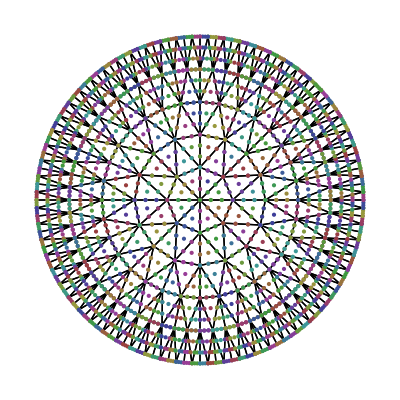

```mathematica
lList={};
j=1;
While[j≤Length[TriElements],
Subscript[l, j]={{TriNodes[[TriElements[[j]][[1]]]][[2]],TriNodes[[TriElements[[j]][[1]]]][[3]]},{TriNodes[[TriElements[[j]][[2]]]][[2]],TriNodes[[TriElements[[j]][[2]]]][[3]]},{TriNodes[[TriElements[[j]][[3]]]][[2]],TriNodes[[TriElements[[j]][[3]]]][[3]]},{TriNodes[[TriElements[[j]][[4]]]][[2]],TriNodes[[TriElements[[j]][[4]]]][[3]]},
{TriNodes[[TriElements[[j]][[5]]]][[2]],TriNodes[[TriElements[[j]][[5]]]][[3]]},{TriNodes[[TriElements[[j]][[6]]]][[2]],TriNodes[[TriElements[[j]][[6]]]][[3]]},{TriNodes[[TriElements[[j]][[7]]]][[2]],TriNodes[[TriElements[[j]][[7]]]][[3]]},{TriNodes[[TriElements[[j]][[8]]]][[2]],TriNodes[[TriElements[[j]][[8]]]][[3]]},{TriNodes[[TriElements[[j]][[9]]]][[2]],TriNodes[[TriElements[[j]][[9]]]][[3]]},{TriNodes[[TriElements[[j]][[1]]]][[2]],TriNodes[[TriElements[[j]][[1]]]][[3]]}};
AppendTo[lList,Subscript[l, j]];
j++;
]
p1=Graphics[Line[lList]];

nodelist={};
jj=1;
While[jj≤Length[TriElements],
Subscript[l, jj]={{TriNodes[[TriElements[[jj]][[1]]]][[2]],TriNodes[[TriElements[[jj]][[1]]]][[3]]},{TriNodes[[TriElements[[jj]][[2]]]][[2]],TriNodes[[TriElements[[jj]][[2]]]][[3]]},{TriNodes[[TriElements[[jj]][[3]]]][[2]],TriNodes[[TriElements[[jj]][[3]]]][[3]]},{TriNodes[[TriElements[[jj]][[4]]]][[2]],TriNodes[[TriElements[[jj]][[4]]]][[3]]},
{TriNodes[[TriElements[[jj]][[5]]]][[2]],TriNodes[[TriElements[[jj]][[5]]]][[3]]},{TriNodes[[TriElements[[jj]][[6]]]][[2]],TriNodes[[TriElements[[jj]][[6]]]][[3]]},{TriNodes[[TriElements[[jj]][[7]]]][[2]],TriNodes[[TriElements[[jj]][[7]]]][[3]]},{TriNodes[[TriElements[[jj]][[8]]]][[2]],TriNodes[[TriElements[[jj]][[8]]]][[3]]},{TriNodes[[TriElements[[jj]][[9]]]][[2]],TriNodes[[TriElements[[jj]][[9]]]][[3]]},{TriNodes[[TriElements[[jj]][[10]]]][[2]],TriNodes[[TriElements[[jj]][[10]]]][[3]]}};
AppendTo[nodelist,Subscript[l, jj]];
jj++;
]
p2=ListPlot[nodelist];
Show[p1,p2]
```

```mathematica
RefTriangle={{0.,0.},1/3{1.,0.},1/3{2.,0.},{1.,0.},1/3{1.,2.},1/3{2.,1.},{0.,1.},1/3{0.,2.},1/3{0.,1.},1/3{1.,1.}};
f[x_,y_]={1,x,y,x^2,x*y,y^2,x^3,x^2*y,x*y^2,y^3};
(*Create Vandermonde Matrix*)
VandermondeMat={};
i=1;
While[i≤Length[RefTriangle],
AppendTo[VandermondeMat,f[RefTriangle[[i]][[1]],RefTriangle[[i]][[2]]]];
i++;
]
Print["Vandermonde Matrix"]
Print[MatrixForm[VandermondeMat]]
```

Vandermonde Matrix

(1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 0.333333 | 0. | 0.111111 | 0. | 0. | 0.037037 | 0. | 0. | 0.
1 | 0.666667 | 0. | 0.444444 | 0. | 0. | 0.296296 | 0. | 0. | 0.
1 | 1. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0.
1 | 0.333333 | 0.666667 | 0.111111 | 0.222222 | 0.444444 | 0.037037 | 0.0740741 | 0.148148 | 0.296296
1 | 0.666667 | 0.333333 | 0.444444 | 0.222222 | 0.111111 | 0.296296 | 0.148148 | 0.0740741 | 0.037037
1 | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 1.
1 | 0. | 0.666667 | 0. | 0. | 0.444444 | 0. | 0. | 0. | 0.296296
1 | 0. | 0.333333 | 0. | 0. | 0.111111 | 0. | 0. | 0. | 0.037037
1 | 0.333333 | 0.333333 | 0.111111 | 0.111111 | 0.111111 | 0.037037 | 0.037037 | 0.037037 | 0.037037)

```mathematica
IDMat=IdentityMatrix[10];
PolyMat={};
ij=1;
While[ij≤Length[RefTriangle],
CoeffMat=LinearSolve[VandermondeMat,IDMat[[ij]]];
Polyct[x_,y_]=CoeffMat.f[x,y];
AppendTo[PolyMat,Polyct[x,y]];
ij++
];
Print["Reference Polynomials"]
Print[PolyMat//MatrixForm]
```

Reference Polynomials

(1.-5.5 x+9. x^2-4.5 x^3-5.5 y+18. x y-13.5 x^2 y+9. y^2-13.5 x y^2-4.5 y^3
0.+9. x-22.5 x^2+13.5 x^3-22.5 x y+27. x^2 y+13.5 x y^2
0.-4.5 x+18. x^2-13.5 x^3+4.5 x y-13.5 x^2 y-1.26461×10^-15 x y^2
0.+1. x-4.5 x^2+4.5 x^3-2.81025×10^-16 x y+4.21538×10^-16 x^2 y+4.21538×10^-16 x y^2
0.-4.5 x y+13.5 x y^2
0.-4.5 x y+13.5 x^2 y
0.+1. y-4.5 y^2+4.5 y^3
0.-4.5 y+4.5 x y+18. y^2-13.5 x y^2-13.5 y^3
0.+9. y-22.5 x y+13.5 x^2 y-22.5 y^2+27. x y^2+13.5 y^3
0.+27. x y-27. x^2 y-27. x y^2)

```mathematica
a=γ-α;
b=δ-β;
c=σ-α;
d=τ-β;
A=({{a, c}, {b, d}});
InvA= Inverse[A];

(*Function for sending Element to the Reference*)

(*xyvar[α_,β_,γ_,δ_,σ_,τ_,x_,y_]=(InvA).{x,y}-(InvA).{α,β} to be replaced by the following:*)
xvar[α_,β_,γ_,δ_,σ_,τ_,x_,y_]=d/Det[A]* x+ -c/Det[A]*y-d/Det[A]*α+c/Det[A]*β;
yvar[α_,β_,γ_,δ_,σ_,τ_,x_,y_]=-b/Det[A]* x+ a/Det[A]*y+b/Det[A]*α-a/Det[A]*β;

(*Reference to Element*)
(*xyinvvar[α_,β_,γ_,δ_,σ_,τ_,x_,y_]=A.{x,y} +{α,β} to be replaced with the following:*)
xinvvar[α_,β_,γ_,δ_,σ_,τ_,x_,y_]=a*x+c*y+α;
yinvvar[α_,β_,γ_,δ_,σ_,τ_,x_,y_]=b*x+d*y+β;


Print["Variable Change transformation for x"];
xvar[α,β,γ,δ,σ,τ,x,y]
Print["Variable Change transformation for y"];
yvar[α,β,γ,δ,σ,τ,x,y]

Print["Inverse Variable Change for x"];
xinvvar[α,β,γ,δ,σ,τ,x,y]//MatrixForm
Print["Inverse Variable Change for y"];
yinvvar[α,β,γ,δ,σ,τ,x,y]//MatrixForm
```

Variable Change transformation for x

-(y (-α+σ))/(-β γ+α δ+β σ-δ σ-α τ+γ τ)+(β (-α+σ))/(-β γ+α δ+β σ-δ σ-α τ+γ τ)+(x (-β+τ))/(-β γ+α δ+β σ-δ σ-α τ+γ τ)-(α (-β+τ))/(-β γ+α δ+β σ-δ σ-α τ+γ τ)

Variable Change transformation for y

(y (-α+γ))/(-β γ+α δ+β σ-δ σ-α τ+γ τ)-(β (-α+γ))/(-β γ+α δ+β σ-δ σ-α τ+γ τ)-(x (-β+δ))/(-β γ+α δ+β σ-δ σ-α τ+γ τ)+(α (-β+δ))/(-β γ+α δ+β σ-δ σ-α τ+γ τ)

Inverse Variable Change for x

α+x (-α+γ)+y (-α+σ)

Inverse Variable Change for y

β+x (-β+δ)+y (-β+τ)

```mathematica
(*Initialize K/ 3 nested loops*)

GlobalK=IdentityMatrix[Length[TriNodes]];
GlobalK=0*GlobalK;
k=1;
element=1;
While[element≤Length[TriElements],
Varα=TriNodes[[TriElements[[element]][[1]]]][[2]];
Varβ=TriNodes[[TriElements[[element]][[1]]]][[3]];
Varγ=TriNodes[[TriElements[[element]][[4]]]][[2]];
Varδ=TriNodes[[TriElements[[element]][[4]]]][[3]];
Varσ=TriNodes[[TriElements[[element]][[7]]]][[2]];
Varτ=TriNodes[[TriElements[[element]][[7]]]][[3]];
xaffine[x_,y_]=xvar[Varα,Varβ,Varγ,Varδ,Varσ,Varτ,x,y];
yaffine[x_,y_]=yvar[Varα,Varβ,Varγ,Varδ,Varσ,Varτ,x,y];

ct1=1;
While[ct1≤Length[TriElements[[1]]],
ϕct[x_,y_]=PolyMat[[ct1]];
ϕref1[x_,y_]=ϕct[xaffine[x,y],yaffine[x,y]];
Laplϕ[x_,y_]=D[ϕref1[x,y],{x,2}]+D[ϕref1[x,y],{y,2}];
RowID=TriElements[[element,ct1]];

ct2=1;
While[ct2≤Length[TriElements[[1]]],
ColID=TriElements[[element,ct2]];
xpt=TriNodes[[TriElements[[element]][[ct2]]]][[2]];
ypt=TriNodes[[TriElements[[element]][[ct2]]]][[3]];
Lapϕloc=Laplϕ[xpt,ypt];
GlobalK[[RowID,ColID]]=Lapϕloc+GlobalK[[RowID,ColID]];
ct2++
];

ct1++
];

element++
];

Print[Lapϕloc]
```

-315.258

```mathematica
(*Create Dirichlet Boundary Conditions*)
GlobalK[[1]]=IdentityMatrix[Length[TriNodes]][[1]];
Print[GlobalK[[1]]//MatrixForm];
```

```mathematica
(* Solve Eigensystem*)
eisys=Eigensystem[GlobalK];

(*Create List of EigenValues of GlobalK*)
lambdas=eisys[[1]];

tuples={};
a=1;
While[a≤Length[TriNodes],
b=lambdas[[a]];
imb:=If[(-.01<Im[b]<.01),0,Im[b]];
bb=Re[b]+(imb)ⅈ;
AppendTo[tuples,{a,bb}];
a++
;
]

lambdas[[1]]
```

1366.78

```mathematica
threetuple={};
node=1;
While[node≤Length[TriNodes],
xcoord=TriNodes[[node]][[2]];
ycoord=TriNodes[[node]][[3]];
AppendTo[threetuple,{xcoord,ycoord,eisys[[2,906,node]]}];
node++
];
threetuple//MatrixForm
```

(0 | 0 | -3.70241×10^-15
0.707107 | 0.707107 | 0.0000615082
0. | 1. | -0.0000615082
-0.707107 | 0.707107 | 0.0000615082
-1. | 0. | -0.0000615082
-0.707107 | -0.707107 | 0.0000615082
0. | -1. | -0.0000615082
0.707107 | -0.707107 | 0.0000615082
1. | 0. | -0.0000615082
1.41421 | 1.41421 | 0.0000387692
0.765367 | 1.84776 | -0.0000554095
0. | 2. | -0.0000387692
-0.765367 | 1.84776 | 0.0000554095
-1.41421 | 1.41421 | 0.0000387692
-1.84776 | 0.765367 | -0.0000554095
-2. | 0. | -0.0000387692
-1.84776 | -0.765367 | 0.0000554095
-1.41421 | -1.41421 | 0.0000387692
-0.765367 | -1.84776 | -0.0000554095
0. | -2. | -0.0000387692
0.765367 | -1.84776 | 0.0000554095
1.41421 | -1.41421 | 0.0000387692
1.84776 | -0.765367 | -0.0000554095
2. | 0. | -0.0000387692
1.84776 | 0.765367 | 0.0000554095
2.12132 | 2.12132 | 0.00014846
1.66671 | 2.49441 | -0.0000449612
1.14805 | 2.77164 | -0.0000446282
0.585271 | 2.94236 | 0.0000948134
0. | 3. | -0.00014846
-0.585271 | 2.94236 | 0.0000449612
-1.14805 | 2.77164 | 0.0000446282
-1.66671 | 2.49441 | -0.0000948134
-2.12132 | 2.12132 | 0.00014846
-2.49441 | 1.66671 | -0.0000449612
-2.77164 | 1.14805 | -0.0000446282
-2.94236 | 0.585271 | 0.0000948134
-3. | 0. | -0.00014846
-2.94236 | -0.585271 | 0.0000449612
-2.77164 | -1.14805 | 0.0000446282
-2.49441 | -1.66671 | -0.0000948134
-2.12132 | -2.12132 | 0.00014846
-1.66671 | -2.49441 | -0.0000449612
-1.14805 | -2.77164 | -0.0000446282
-0.585271 | -2.94236 | 0.0000948134
0. | -3. | -0.00014846
0.585271 | -2.94236 | 0.0000449612
1.14805 | -2.77164 | 0.0000446282
1.66671 | -2.49441 | -0.0000948134
2.12132 | -2.12132 | 0.00014846
2.49441 | -1.66671 | -0.0000449612
2.77164 | -1.14805 | -0.0000446282
2.94236 | -0.585271 | 0.0000948134
3. | 0. | -0.00014846
2.94236 | 0.585271 | 0.0000449612
2.77164 | 1.14805 | 0.0000446282
2.49441 | 1.66671 | -0.0000948134
2.82843 | 2.82843 | -0.0000439269
2.53757 | 3.09204 | -0.0000974573
2.22228 | 3.32588 | 0.0000818999
1.88559 | 3.52769 | 0.000138413
1.53073 | 3.69552 | 0.0000598935
1.16114 | 3.82776 | -0.000109496
0.780361 | 3.92314 | -0.000237246
0.392069 | 3.98074 | 0.000164898
0. | 4. | 0.0000439269
-0.392069 | 3.98074 | 0.0000974573
-0.780361 | 3.92314 | -0.0000818999
-1.16114 | 3.82776 | -0.000138413
-1.53073 | 3.69552 | -0.0000598935
-1.88559 | 3.52769 | 0.000109496
-2.22228 | 3.32588 | 0.000237246
-2.53757 | 3.09204 | -0.000164898
-2.82843 | 2.82843 | -0.0000439269
-3.09204 | 2.53757 | -0.0000974573
-3.32588 | 2.22228 | 0.0000818999
-3.52769 | 1.88559 | 0.000138413
-3.69552 | 1.53073 | 0.0000598935
-3.82776 | 1.16114 | -0.000109496
-3.92314 | 0.780361 | -0.000237246
-3.98074 | 0.392069 | 0.000164898
-4. | 0. | 0.0000439269
-3.98074 | -0.392069 | 0.0000974573
-3.92314 | -0.780361 | -0.0000818999
-3.82776 | -1.16114 | -0.000138413
-3.69552 | -1.53073 | -0.0000598935
-3.52769 | -1.88559 | 0.000109496
-3.32588 | -2.22228 | 0.000237246
-3.09204 | -2.53757 | -0.000164898
-2.82843 | -2.82843 | -0.0000439269
-2.53757 | -3.09204 | -0.0000974573
-2.22228 | -3.32588 | 0.0000818999
-1.88559 | -3.52769 | 0.000138413
-1.53073 | -3.69552 | 0.0000598935
-1.16114 | -3.82776 | -0.000109496
-0.780361 | -3.92314 | -0.000237246
-0.392069 | -3.98074 | 0.000164898
0. | -4. | 0.0000439269
0.392069 | -3.98074 | 0.0000974573
0.780361 | -3.92314 | -0.0000818999
1.16114 | -3.82776 | -0.000138413
1.53073 | -3.69552 | -0.0000598935
1.88559 | -3.52769 | 0.000109496
2.22228 | -3.32588 | 0.000237246
2.53757 | -3.09204 | -0.000164898
2.82843 | -2.82843 | -0.0000439269
3.09204 | -2.53757 | -0.0000974573
3.32588 | -2.22228 | 0.0000818999
3.52769 | -1.88559 | 0.000138413
3.69552 | -1.53073 | 0.0000598935
3.82776 | -1.16114 | -0.000109496
3.92314 | -0.780361 | -0.000237246
3.98074 | -0.392069 | 0.000164898
4. | 0. | 0.0000439269
3.98074 | 0.392069 | 0.0000974573
3.92314 | 0.780361 | -0.0000818999
3.82776 | 1.16114 | -0.000138413
3.69552 | 1.53073 | -0.0000598935
3.52769 | 1.88559 | 0.000109496
3.32588 | 2.22228 | 0.000237246
3.09204 | 2.53757 | -0.000164898
3.53553 | 3.53553 | 0.0000707454
3.35779 | 3.70476 | 0.000261175
3.17197 | 3.86505 | -0.000247802
2.9785 | 4.01604 | -0.0000264204
2.77785 | 4.15735 | 0.0000915871
2.57051 | 4.28864 | -0.00023795
2.35698 | 4.40961 | 0.000602572
2.13778 | 4.51995 | 0.0000486845
1.91342 | 4.6194 | 0.000672837
1.68445 | 4.70772 | 0.000106416
1.45142 | 4.7847 | -0.000698164
1.2149 | 4.85016 | -0.0000840649
0.975452 | 4.90393 | -0.00152893
0.733652 | 4.94588 | 0.000123169
0.490086 | 4.97592 | 0.00141182
0.245338 | 4.99398 | 0.0000504427
0. | 5. | -0.0000707454
-0.245338 | 4.99398 | -0.000261175
-0.490086 | 4.97592 | 0.000247802
-0.733652 | 4.94588 | 0.0000264204
-0.975452 | 4.90393 | -0.0000915871
-1.2149 | 4.85016 | 0.00023795
-1.45142 | 4.7847 | -0.000602572
-1.68445 | 4.70772 | -0.0000486845
-1.91342 | 4.6194 | -0.000672837
-2.13778 | 4.51995 | -0.000106416
-2.35698 | 4.40961 | 0.000698164
-2.57051 | 4.28864 | 0.0000840649
-2.77785 | 4.15735 | 0.00152893
-2.9785 | 4.01604 | -0.000123169
-3.17197 | 3.86505 | -0.00141182
-3.35779 | 3.70476 | -0.0000504427
-3.53553 | 3.53553 | 0.0000707454
-3.70476 | 3.35779 | 0.000261175
-3.86505 | 3.17197 | -0.000247802
-4.01604 | 2.9785 | -0.0000264204
-4.15735 | 2.77785 | 0.0000915871
-4.28864 | 2.57051 | -0.00023795
-4.40961 | 2.35698 | 0.000602572
-4.51995 | 2.13778 | 0.0000486845
-4.6194 | 1.91342 | 0.000672837
-4.70772 | 1.68445 | 0.000106416
-4.7847 | 1.45142 | -0.000698164
-4.85016 | 1.2149 | -0.0000840649
-4.90393 | 0.975452 | -0.00152893
-4.94588 | 0.733652 | 0.000123169
-4.97592 | 0.490086 | 0.00141182
-4.99398 | 0.245338 | 0.0000504427
-5. | 0. | -0.0000707454
-4.99398 | -0.245338 | -0.000261175
-4.97592 | -0.490086 | 0.000247802
-4.94588 | -0.733652 | 0.0000264204
-4.90393 | -0.975452 | -0.0000915871
-4.85016 | -1.2149 | 0.00023795
-4.7847 | -1.45142 | -0.000602572
-4.70772 | -1.68445 | -0.0000486845
-4.6194 | -1.91342 | -0.000672837
-4.51995 | -2.13778 | -0.000106416
-4.40961 | -2.35698 | 0.000698164
-4.28864 | -2.57051 | 0.0000840649
-4.15735 | -2.77785 | 0.00152893
-4.01604 | -2.9785 | -0.000123169
-3.86505 | -3.17197 | -0.00141182
-3.70476 | -3.35779 | -0.0000504427
-3.53553 | -3.53553 | 0.0000707454
-3.35779 | -3.70476 | 0.000261175
-3.17197 | -3.86505 | -0.000247802
-2.9785 | -4.01604 | -0.0000264204
-2.77785 | -4.15735 | 0.0000915871
-2.57051 | -4.28864 | -0.00023795
-2.35698 | -4.40961 | 0.000602572
-2.13778 | -4.51995 | 0.0000486845
-1.91342 | -4.6194 | 0.000672837
-1.68445 | -4.70772 | 0.000106416
-1.45142 | -4.7847 | -0.000698164
-1.2149 | -4.85016 | -0.0000840649
-0.975452 | -4.90393 | -0.00152893
-0.733652 | -4.94588 | 0.000123169
-0.490086 | -4.97592 | 0.00141182
-0.245338 | -4.99398 | 0.0000504427
0. | -5. | -0.0000707454
0.245338 | -4.99398 | -0.000261175
0.490086 | -4.97592 | 0.000247802
0.733652 | -4.94588 | 0.0000264204
0.975452 | -4.90393 | -0.0000915871
1.2149 | -4.85016 | 0.00023795
1.45142 | -4.7847 | -0.000602572
1.68445 | -4.70772 | -0.0000486845
1.91342 | -4.6194 | -0.000672837
2.13778 | -4.51995 | -0.000106416
2.35698 | -4.40961 | 0.000698164
2.57051 | -4.28864 | 0.0000840649
2.77785 | -4.15735 | 0.00152893
2.9785 | -4.01604 | -0.000123169
3.17197 | -3.86505 | -0.00141182
3.35779 | -3.70476 | -0.0000504427
3.53553 | -3.53553 | 0.0000707454
3.70476 | -3.35779 | 0.000261175
3.86505 | -3.17197 | -0.000247802
4.01604 | -2.9785 | -0.0000264204
4.15735 | -2.77785 | 0.0000915871
4.28864 | -2.57051 | -0.00023795
4.40961 | -2.35698 | 0.000602572
4.51995 | -2.13778 | 0.0000486845
4.6194 | -1.91342 | 0.000672837
4.70772 | -1.68445 | 0.000106416
4.7847 | -1.45142 | -0.000698164
4.85016 | -1.2149 | -0.0000840649
4.90393 | -0.975452 | -0.00152893
4.94588 | -0.733652 | 0.000123169
4.97592 | -0.490086 | 0.00141182
4.99398 | -0.245338 | 0.0000504427
5. | 0. | -0.0000707454
4.99398 | 0.245338 | -0.000261175
4.97592 | 0.490086 | 0.000247802
4.94588 | 0.733652 | 0.0000264204
4.90393 | 0.975452 | -0.0000915871
4.85016 | 1.2149 | 0.00023795
4.7847 | 1.45142 | -0.000602572
4.70772 | 1.68445 | -0.0000486845
4.6194 | 1.91342 | -0.000672837
4.51995 | 2.13778 | -0.000106416
4.40961 | 2.35698 | 0.000698164
4.28864 | 2.57051 | 0.0000840649
4.15735 | 2.77785 | 0.00152893
4.01604 | 2.9785 | -0.000123169
3.86505 | 3.17197 | -0.00141182
3.70476 | 3.35779 | -0.0000504427
0.235702 | 0.235702 | -0.0000630254
0.471405 | 0.471405 | 0.0000630254
0.471405 | 0.804738 | -0.000259748
0.235702 | 0.902369 | 0.000259748
0. | 0.666667 | -0.0000630254
0. | 0.333333 | 0.0000630254
0.235702 | 0.569036 | 6.49583×10^-13
0. | 0.333333 | 0.0000630254
0. | 0.666667 | -0.0000630254
-0.235702 | 0.902369 | 0.000259748
-0.471405 | 0.804738 | -0.000259748
-0.471405 | 0.471405 | 0.0000630254
-0.235702 | 0.235702 | -0.0000630254
-0.235702 | 0.569036 | 2.20334×10^-12
-0.235702 | 0.235702 | -0.0000630254
-0.471405 | 0.471405 | 0.0000630254
-0.804738 | 0.471405 | -0.000259748
-0.902369 | 0.235702 | 0.000259748
-0.666667 | 0. | -0.0000630254
-0.333333 | 0. | 0.0000630254
-0.569036 | 0.235702 | 2.66917×10^-13
-0.333333 | 0. | 0.0000630254
-0.666667 | 0. | -0.0000630254
-0.902369 | -0.235702 | 0.000259748
-0.804738 | -0.471405 | -0.000259748
-0.471405 | -0.471405 | 0.0000630254
-0.235702 | -0.235702 | -0.0000630254
-0.569036 | -0.235702 | -2.21772×10^-13
-0.235702 | -0.235702 | -0.0000630254
-0.471405 | -0.471405 | 0.0000630254
-0.471405 | -0.804738 | -0.000259748
-0.235702 | -0.902369 | 0.000259748
0. | -0.666667 | -0.0000630254
0. | -0.333333 | 0.0000630254
-0.235702 | -0.569036 | 1.27853×10^-13
0. | -0.333333 | 0.0000630254
0. | -0.666667 | -0.0000630254
0.235702 | -0.902369 | 0.000259748
0.471405 | -0.804738 | -0.000259748
0.471405 | -0.471405 | 0.0000630254
0.235702 | -0.235702 | -0.0000630254
0.235702 | -0.569036 | -6.70548×10^-13
0.235702 | -0.235702 | -0.0000630254
0.471405 | -0.471405 | 0.0000630254
0.804738 | -0.471405 | -0.000259748
0.902369 | -0.235702 | 0.000259748
0.666667 | 0. | -0.0000630254
0.333333 | 0. | 0.0000630254
0.569036 | -0.235702 | -8.47375×10^-13
0.333333 | 0. | 0.0000630254
0.666667 | 0. | -0.0000630254
0.902369 | 0.235702 | 0.000259748
0.804738 | 0.471405 | -0.000259748
0.471405 | 0.471405 | 0.0000630254
0.235702 | 0.235702 | -0.0000630254
0.569036 | 0.235702 | -1.15635×10^-12
0.942809 | 0.942809 | 0.0000189002
1.17851 | 1.17851 | 0.000570022
1.19793 | 1.55873 | 0.000114561
0.981649 | 1.70324 | 0.000255585
0.745947 | 1.46754 | 0.000540215
0.726527 | 1.08732 | 0.000219059
0.962229 | 1.32303 | -0.0016889
0.726527 | 1.08732 | 0.000115708
0.745947 | 1.46754 | -0.0000139679
0.510245 | 1.56517 | 0.000216598
0.255122 | 1.28259 | -0.000114858
0.235702 | 0.902369 | 0.000326015
0.471405 | 0.804738 | -0.000247109
0.490825 | 1.18496 | -0.00022209
0.255122 | 1.28259 | -0.00033167
0.510245 | 1.56517 | -0.000890565
0.510245 | 1.89851 | -8.00408×10^-6
0.255122 | 1.94925 | -0.000547448
0. | 1.66667 | -0.000731512
0. | 1.33333 | -0.000198821
0.255122 | 1.61592 | 0.00273637
0. | 1.33333 | -0.0000189002
0. | 1.66667 | -0.000570022
-0.255122 | 1.94925 | -0.000114561
-0.510245 | 1.89851 | -0.000255585
-0.510245 | 1.56517 | -0.000540215
-0.255122 | 1.28259 | -0.000219059
-0.255122 | 1.61592 | 0.0016889
-0.255122 | 1.28259 | -0.000115708
-0.510245 | 1.56517 | 0.0000139679
-0.745947 | 1.46754 | -0.000216598
-0.726527 | 1.08732 | 0.000114858
-0.471405 | 0.804738 | -0.000326015
-0.235702 | 0.902369 | 0.000247109
-0.490825 | 1.18496 | 0.00022209
-0.726527 | 1.08732 | 0.00033167
-0.745947 | 1.46754 | 0.000890565
-0.981649 | 1.70324 | 8.00408×10^-6
-1.19793 | 1.55873 | 0.000547448
-1.17851 | 1.17851 | 0.000731512
-0.942809 | 0.942809 | 0.000198821
-0.962229 | 1.32303 | -0.00273637
-0.942809 | 0.942809 | 0.0000189002
-1.17851 | 1.17851 | 0.000570022
-1.55873 | 1.19793 | 0.000114561
-1.70324 | 0.981649 | 0.000255585
-1.46754 | 0.745947 | 0.000540215
-1.08732 | 0.726527 | 0.000219059
-1.32303 | 0.962229 | -0.0016889
-1.08732 | 0.726527 | 0.000115708
-1.46754 | 0.745947 | -0.0000139679
-1.56517 | 0.510245 | 0.000216598
-1.28259 | 0.255122 | -0.000114858
-0.902369 | 0.235702 | 0.000326015
-0.804738 | 0.471405 | -0.000247109
-1.18496 | 0.490825 | -0.00022209
-1.28259 | 0.255122 | -0.00033167
-1.56517 | 0.510245 | -0.000890565
-1.89851 | 0.510245 | -8.00408×10^-6
-1.94925 | 0.255122 | -0.000547448
-1.66667 | 0. | -0.000731512
-1.33333 | 0. | -0.000198821
-1.61592 | 0.255122 | 0.00273637
-1.33333 | 0. | -0.0000189002
-1.66667 | 0. | -0.000570022
-1.94925 | -0.255122 | -0.000114561
-1.89851 | -0.510245 | -0.000255585
-1.56517 | -0.510245 | -0.000540215
-1.28259 | -0.255122 | -0.000219059
-1.61592 | -0.255122 | 0.0016889
-1.28259 | -0.255122 | -0.000115708
-1.56517 | -0.510245 | 0.0000139679
-1.46754 | -0.745947 | -0.000216598
-1.08732 | -0.726527 | 0.000114858
-0.804738 | -0.471405 | -0.000326015
-0.902369 | -0.235702 | 0.000247109
-1.18496 | -0.490825 | 0.00022209
-1.08732 | -0.726527 | 0.00033167
-1.46754 | -0.745947 | 0.000890565
-1.70324 | -0.981649 | 8.00408×10^-6
-1.55873 | -1.19793 | 0.000547448
-1.17851 | -1.17851 | 0.000731512
-0.942809 | -0.942809 | 0.000198821
-1.32303 | -0.962229 | -0.00273637
-0.942809 | -0.942809 | 0.0000189002
-1.17851 | -1.17851 | 0.000570022
-1.19793 | -1.55873 | 0.000114561
-0.981649 | -1.70324 | 0.000255585
-0.745947 | -1.46754 | 0.000540215
-0.726527 | -1.08732 | 0.000219059
-0.962229 | -1.32303 | -0.0016889
-0.726527 | -1.08732 | 0.000115708
-0.745947 | -1.46754 | -0.0000139679
-0.510245 | -1.56517 | 0.000216598
-0.255122 | -1.28259 | -0.000114858
-0.235702 | -0.902369 | 0.000326015
-0.471405 | -0.804738 | -0.000247109
-0.490825 | -1.18496 | -0.00022209
-0.255122 | -1.28259 | -0.00033167
-0.510245 | -1.56517 | -0.000890565
-0.510245 | -1.89851 | -8.00408×10^-6
-0.255122 | -1.94925 | -0.000547448
0. | -1.66667 | -0.000731512
0. | -1.33333 | -0.000198821
-0.255122 | -1.61592 | 0.00273637
0. | -1.33333 | -0.0000189002
0. | -1.66667 | -0.000570022
0.255122 | -1.94925 | -0.000114561
0.510245 | -1.89851 | -0.000255585
0.510245 | -1.56517 | -0.000540215
0.255122 | -1.28259 | -0.000219059
0.255122 | -1.61592 | 0.0016889
0.255122 | -1.28259 | -0.000115708
0.510245 | -1.56517 | 0.0000139679
0.745947 | -1.46754 | -0.000216598
0.726527 | -1.08732 | 0.000114858
0.471405 | -0.804738 | -0.000326015
0.235702 | -0.902369 | 0.000247109
0.490825 | -1.18496 | 0.00022209
0.726527 | -1.08732 | 0.00033167
0.745947 | -1.46754 | 0.000890565
0.981649 | -1.70324 | 8.00408×10^-6
1.19793 | -1.55873 | 0.000547448
1.17851 | -1.17851 | 0.000731512
0.942809 | -0.942809 | 0.000198821
0.962229 | -1.32303 | -0.00273637
0.942809 | -0.942809 | 0.0000189002
1.17851 | -1.17851 | 0.000570022
1.55873 | -1.19793 | 0.000114561
1.70324 | -0.981649 | 0.000255585
1.46754 | -0.745947 | 0.000540215
1.08732 | -0.726527 | 0.000219059
1.32303 | -0.962229 | -0.0016889
1.08732 | -0.726527 | 0.000115708
1.46754 | -0.745947 | -0.0000139679
1.56517 | -0.510245 | 0.000216598
1.28259 | -0.255122 | -0.000114858
0.902369 | -0.235702 | 0.000326015
0.804738 | -0.471405 | -0.000247109
1.18496 | -0.490825 | -0.00022209
1.28259 | -0.255122 | -0.00033167
1.56517 | -0.510245 | -0.000890565
1.89851 | -0.510245 | -8.00408×10^-6
1.94925 | -0.255122 | -0.000547448
1.66667 | 0. | -0.000731512
1.33333 | 0. | -0.000198821
1.61592 | -0.255122 | 0.00273637
1.33333 | 0. | -0.0000189002
1.66667 | 0. | -0.000570022
1.94925 | 0.255122 | -0.000114561
1.89851 | 0.510245 | -0.000255585
1.56517 | 0.510245 | -0.000540215
1.28259 | 0.255122 | -0.000219059
1.61592 | 0.255122 | 0.0016889
1.28259 | 0.255122 | -0.000115708
1.56517 | 0.510245 | 0.0000139679
1.46754 | 0.745947 | -0.000216598
1.08732 | 0.726527 | 0.000114858
0.804738 | 0.471405 | -0.000326015
0.902369 | 0.235702 | 0.000247109
1.18496 | 0.490825 | 0.00022209
1.08732 | 0.726527 | 0.00033167
1.46754 | 0.745947 | 0.000890565
1.70324 | 0.981649 | 8.00408×10^-6
1.55873 | 1.19793 | 0.000547448
1.17851 | 1.17851 | 0.000731512
0.942809 | 0.942809 | 0.000198821
1.32303 | 0.962229 | -0.00273637
1.64992 | 1.64992 | 0.000113354
1.88562 | 1.88562 | 0.0015056
1.96978 | 2.24568 | 0.000190136
1.81825 | 2.37005 | 0.000359772
1.58254 | 2.13434 | 0.00153401
1.49838 | 1.77428 | 0.000461775
1.73408 | 2.00998 | -0.00417998
1.49838 | 1.77428 | 0.0000867955
1.58254 | 2.13434 | -0.0000437194
1.36626 | 2.27886 | 0.000182702
1.06581 | 2.06331 | -0.000139626
0.981649 | 1.70324 | 0.000268466
1.19793 | 1.55873 | -0.000217042
1.2821 | 1.91879 | -0.0000779742
1.06581 | 2.06331 | -0.000433601
1.36626 | 2.27886 | -0.00166429
1.49382 | 2.58682 | -0.0000355839
1.32094 | 2.67923 | -0.000545534
1.02049 | 2.46368 | -0.00157399
0.892928 | 2.15572 | -0.000128591
1.19338 | 2.37127 | 0.00439343
0.892928 | 2.15572 | 0.0000125296
1.02049 | 2.46368 | -0.00100633
0.960457 | 2.82854 | -0.0000686832
0.772864 | 2.88545 | -0.000318718
0.645303 | 2.57749 | -0.000962061
0.705335 | 2.21262 | -0.000245489
0.832896 | 2.52058 | 0.00252197
0.705335 | 2.21262 | -0.000394125
0.645303 | 2.57749 | -0.0000712159
0.390181 | 2.62824 | -0.000480693
0.19509 | 2.31412 | 0.0000153515
0.255122 | 1.94925 | -0.000347084
0.510245 | 1.89851 | 0.0000911474
0.450213 | 2.26337 | 0.00113583
0.19509 | 2.31412 | -0.000394683
0.390181 | 2.62824 | -0.00128355
0.390181 | 2.96157 | -0.000460755
0.19509 | 2.98079 | -0.0000200612
0. | 2.66667 | -0.00130314
0. | 2.33333 | -0.0000630213
0.19509 | 2.64745 | 0.0035125
0. | 2.33333 | -0.000113354
0. | 2.66667 | -0.0015056
-0.19509 | 2.98079 | -0.000190136
-0.390181 | 2.96157 | -0.000359772
-0.390181 | 2.62824 | -0.00153401
-0.19509 | 2.31412 | -0.000461775
-0.19509 | 2.64745 | 0.00417998
-0.19509 | 2.31412 | -0.0000867955
-0.390181 | 2.62824 | 0.0000437194
-0.645303 | 2.57749 | -0.000182702
-0.705335 | 2.21262 | 0.000139626
-0.510245 | 1.89851 | -0.000268466
-0.255122 | 1.94925 | 0.000217042
-0.450213 | 2.26337 | 0.0000779742
-0.705335 | 2.21262 | 0.000433601
-0.645303 | 2.57749 | 0.00166429
-0.772864 | 2.88545 | 0.0000355839
-0.960457 | 2.82854 | 0.000545534
-1.02049 | 2.46368 | 0.00157399
-0.892928 | 2.15572 | 0.000128591
-0.832896 | 2.52058 | -0.00439343
-0.892928 | 2.15572 | -0.0000125296
-1.02049 | 2.46368 | 0.00100633
-1.32094 | 2.67923 | 0.0000686832
-1.49382 | 2.58682 | 0.000318718
-1.36626 | 2.27886 | 0.000962061
-1.06581 | 2.06331 | 0.000245489
-1.19338 | 2.37127 | -0.00252197
-1.06581 | 2.06331 | 0.000394125
-1.36626 | 2.27886 | 0.0000712159
-1.58254 | 2.13434 | 0.000480693
-1.49838 | 1.77428 | -0.0000153515
-1.19793 | 1.55873 | 0.000347084
-0.981649 | 1.70324 | -0.0000911474
-1.2821 | 1.91879 | -0.00113583
-1.49838 | 1.77428 | 0.000394683
-1.58254 | 2.13434 | 0.00128355
-1.81825 | 2.37005 | 0.000460755
-1.96978 | 2.24568 | 0.0000200612
-1.88562 | 1.88562 | 0.00130314
-1.64992 | 1.64992 | 0.0000630213
-1.73408 | 2.00998 | -0.0035125
-1.64992 | 1.64992 | 0.000113354
-1.88562 | 1.88562 | 0.0015056
-2.24568 | 1.96978 | 0.000190136
-2.37005 | 1.81825 | 0.000359772
-2.13434 | 1.58254 | 0.00153401
-1.77428 | 1.49838 | 0.000461775
-2.00998 | 1.73408 | -0.00417998
-1.77428 | 1.49838 | 0.0000867955
-2.13434 | 1.58254 | -0.0000437194
-2.27886 | 1.36626 | 0.000182702
-2.06331 | 1.06581 | -0.000139626
-1.70324 | 0.981649 | 0.000268466
-1.55873 | 1.19793 | -0.000217042
-1.91879 | 1.2821 | -0.0000779742
-2.06331 | 1.06581 | -0.000433601
-2.27886 | 1.36626 | -0.00166429
-2.58682 | 1.49382 | -0.0000355839
-2.67923 | 1.32094 | -0.000545534
-2.46368 | 1.02049 | -0.00157399
-2.15572 | 0.892928 | -0.000128591
-2.37127 | 1.19338 | 0.00439343
-2.15572 | 0.892928 | 0.0000125296
-2.46368 | 1.02049 | -0.00100633
-2.82854 | 0.960457 | -0.0000686832
-2.88545 | 0.772864 | -0.000318718
-2.57749 | 0.645303 | -0.000962061
-2.21262 | 0.705335 | -0.000245489
-2.52058 | 0.832896 | 0.00252197
-2.21262 | 0.705335 | -0.000394125
-2.57749 | 0.645303 | -0.0000712159
-2.62824 | 0.390181 | -0.000480693
-2.31412 | 0.19509 | 0.0000153515
-1.94925 | 0.255122 | -0.000347084
-1.89851 | 0.510245 | 0.0000911474
-2.26337 | 0.450213 | 0.00113583
-2.31412 | 0.19509 | -0.000394683
-2.62824 | 0.390181 | -0.00128355
-2.96157 | 0.390181 | -0.000460755
-2.98079 | 0.19509 | -0.0000200612
-2.66667 | 0. | -0.00130314
-2.33333 | 0. | -0.0000630213
-2.64745 | 0.19509 | 0.0035125
-2.33333 | 0. | -0.000113354
-2.66667 | 0. | -0.0015056
-2.98079 | -0.19509 | -0.000190136
-2.96157 | -0.390181 | -0.000359772
-2.62824 | -0.390181 | -0.00153401
-2.31412 | -0.19509 | -0.000461775
-2.64745 | -0.19509 | 0.00417998
-2.31412 | -0.19509 | -0.0000867955
-2.62824 | -0.390181 | 0.0000437194
-2.57749 | -0.645303 | -0.000182702
-2.21262 | -0.705335 | 0.000139626
-1.89851 | -0.510245 | -0.000268466
-1.94925 | -0.255122 | 0.000217042
-2.26337 | -0.450213 | 0.0000779742
-2.21262 | -0.705335 | 0.000433601
-2.57749 | -0.645303 | 0.00166429
-2.88545 | -0.772864 | 0.0000355839
-2.82854 | -0.960457 | 0.000545534
-2.46368 | -1.02049 | 0.00157399
-2.15572 | -0.892928 | 0.000128591
-2.52058 | -0.832896 | -0.00439343
-2.15572 | -0.892928 | -0.0000125296
-2.46368 | -1.02049 | 0.00100633
-2.67923 | -1.32094 | 0.0000686832
-2.58682 | -1.49382 | 0.000318718
-2.27886 | -1.36626 | 0.000962061
-2.06331 | -1.06581 | 0.000245489
-2.37127 | -1.19338 | -0.00252197
-2.06331 | -1.06581 | 0.000394125
-2.27886 | -1.36626 | 0.0000712159
-2.13434 | -1.58254 | 0.000480693
-1.77428 | -1.49838 | -0.0000153515
-1.55873 | -1.19793 | 0.000347084
-1.70324 | -0.981649 | -0.0000911474
-1.91879 | -1.2821 | -0.00113583
-1.77428 | -1.49838 | 0.000394683
-2.13434 | -1.58254 | 0.00128355
-2.37005 | -1.81825 | 0.000460755
-2.24568 | -1.96978 | 0.0000200612
-1.88562 | -1.88562 | 0.00130314
-1.64992 | -1.64992 | 0.0000630213
-2.00998 | -1.73408 | -0.0035125
-1.64992 | -1.64992 | 0.000113354
-1.88562 | -1.88562 | 0.0015056
-1.96978 | -2.24568 | 0.000190136
-1.81825 | -2.37005 | 0.000359772
-1.58254 | -2.13434 | 0.00153401
-1.49838 | -1.77428 | 0.000461775
-1.73408 | -2.00998 | -0.00417998
-1.49838 | -1.77428 | 0.0000867955
-1.58254 | -2.13434 | -0.0000437194
-1.36626 | -2.27886 | 0.000182702
-1.06581 | -2.06331 | -0.000139626
-0.981649 | -1.70324 | 0.000268466
-1.19793 | -1.55873 | -0.000217042
-1.2821 | -1.91879 | -0.0000779742
-1.06581 | -2.06331 | -0.000433601
-1.36626 | -2.27886 | -0.00166429
-1.49382 | -2.58682 | -0.0000355839
-1.32094 | -2.67923 | -0.000545534
-1.02049 | -2.46368 | -0.00157399
-0.892928 | -2.15572 | -0.000128591
-1.19338 | -2.37127 | 0.00439343
-0.892928 | -2.15572 | 0.0000125296
-1.02049 | -2.46368 | -0.00100633
-0.960457 | -2.82854 | -0.0000686832
-0.772864 | -2.88545 | -0.000318718
-0.645303 | -2.57749 | -0.000962061
-0.705335 | -2.21262 | -0.000245489
-0.832896 | -2.52058 | 0.00252197
-0.705335 | -2.21262 | -0.000394125
-0.645303 | -2.57749 | -0.0000712159
-0.390181 | -2.62824 | -0.000480693
-0.19509 | -2.31412 | 0.0000153515
-0.255122 | -1.94925 | -0.000347084
-0.510245 | -1.89851 | 0.0000911474
-0.450213 | -2.26337 | 0.00113583
-0.19509 | -2.31412 | -0.000394683
-0.390181 | -2.62824 | -0.00128355
-0.390181 | -2.96157 | -0.000460755
-0.19509 | -2.98079 | -0.0000200612
0. | -2.66667 | -0.00130314
0. | -2.33333 | -0.0000630213
-0.19509 | -2.64745 | 0.0035125
0. | -2.33333 | -0.000113354
0. | -2.66667 | -0.0015056
0.19509 | -2.98079 | -0.000190136
0.390181 | -2.96157 | -0.000359772
0.390181 | -2.62824 | -0.00153401
0.19509 | -2.31412 | -0.000461775
0.19509 | -2.64745 | 0.00417998
0.19509 | -2.31412 | -0.0000867955
0.390181 | -2.62824 | 0.0000437194
0.645303 | -2.57749 | -0.000182702
0.705335 | -2.21262 | 0.000139626
0.510245 | -1.89851 | -0.000268466
0.255122 | -1.94925 | 0.000217042
0.450213 | -2.26337 | 0.0000779742
0.705335 | -2.21262 | 0.000433601
0.645303 | -2.57749 | 0.00166429
0.772864 | -2.88545 | 0.0000355839
0.960457 | -2.82854 | 0.000545534
1.02049 | -2.46368 | 0.00157399
0.892928 | -2.15572 | 0.000128591
0.832896 | -2.52058 | -0.00439343
0.892928 | -2.15572 | -0.0000125296
1.02049 | -2.46368 | 0.00100633
1.32094 | -2.67923 | 0.0000686832
1.49382 | -2.58682 | 0.000318718
1.36626 | -2.27886 | 0.000962061
1.06581 | -2.06331 | 0.000245489
1.19338 | -2.37127 | -0.00252197
1.06581 | -2.06331 | 0.000394125
1.36626 | -2.27886 | 0.0000712159
1.58254 | -2.13434 | 0.000480693
1.49838 | -1.77428 | -0.0000153515
1.19793 | -1.55873 | 0.000347084
0.981649 | -1.70324 | -0.0000911474
1.2821 | -1.91879 | -0.00113583
1.49838 | -1.77428 | 0.000394683
1.58254 | -2.13434 | 0.00128355
1.81825 | -2.37005 | 0.000460755
1.96978 | -2.24568 | 0.0000200612
1.88562 | -1.88562 | 0.00130314
1.64992 | -1.64992 | 0.0000630213
1.73408 | -2.00998 | -0.0035125
1.64992 | -1.64992 | 0.000113354
1.88562 | -1.88562 | 0.0015056
2.24568 | -1.96978 | 0.000190136
2.37005 | -1.81825 | 0.000359772
2.13434 | -1.58254 | 0.00153401
1.77428 | -1.49838 | 0.000461775
2.00998 | -1.73408 | -0.00417998
1.77428 | -1.49838 | 0.0000867955
2.13434 | -1.58254 | -0.0000437194
2.27886 | -1.36626 | 0.000182702
2.06331 | -1.06581 | -0.000139626
1.70324 | -0.981649 | 0.000268466
1.55873 | -1.19793 | -0.000217042
1.91879 | -1.2821 | -0.0000779742
2.06331 | -1.06581 | -0.000433601
2.27886 | -1.36626 | -0.00166429
2.58682 | -1.49382 | -0.0000355839
2.67923 | -1.32094 | -0.000545534
2.46368 | -1.02049 | -0.00157399
2.15572 | -0.892928 | -0.000128591
2.37127 | -1.19338 | 0.00439343
2.15572 | -0.892928 | 0.0000125296
2.46368 | -1.02049 | -0.00100633
2.82854 | -0.960457 | -0.0000686832
2.88545 | -0.772864 | -0.000318718
2.57749 | -0.645303 | -0.000962061
2.21262 | -0.705335 | -0.000245489
2.52058 | -0.832896 | 0.00252197
2.21262 | -0.705335 | -0.000394125
2.57749 | -0.645303 | -0.0000712159
2.62824 | -0.390181 | -0.000480693
2.31412 | -0.19509 | 0.0000153515
1.94925 | -0.255122 | -0.000347084
1.89851 | -0.510245 | 0.0000911474
2.26337 | -0.450213 | 0.00113583
2.31412 | -0.19509 | -0.000394683
2.62824 | -0.390181 | -0.00128355
2.96157 | -0.390181 | -0.000460755
2.98079 | -0.19509 | -0.0000200612
2.66667 | 0. | -0.00130314
2.33333 | 0. | -0.0000630213
2.64745 | -0.19509 | 0.0035125
2.33333 | 0. | -0.000113354
2.66667 | 0. | -0.0015056
2.98079 | 0.19509 | -0.000190136
2.96157 | 0.390181 | -0.000359772
2.62824 | 0.390181 | -0.00153401
2.31412 | 0.19509 | -0.000461775
2.64745 | 0.19509 | 0.00417998
2.31412 | 0.19509 | -0.0000867955
2.62824 | 0.390181 | 0.0000437194
2.57749 | 0.645303 | -0.000182702
2.21262 | 0.705335 | 0.000139626
1.89851 | 0.510245 | -0.000268466
1.94925 | 0.255122 | 0.000217042
2.26337 | 0.450213 | 0.0000779742
2.21262 | 0.705335 | 0.000433601
2.57749 | 0.645303 | 0.00166429
2.88545 | 0.772864 | 0.0000355839
2.82854 | 0.960457 | 0.000545534
2.46368 | 1.02049 | 0.00157399
2.15572 | 0.892928 | 0.000128591
2.52058 | 0.832896 | -0.00439343
2.15572 | 0.892928 | -0.0000125296
2.46368 | 1.02049 | 0.00100633
2.67923 | 1.32094 | 0.0000686832
2.58682 | 1.49382 | 0.000318718
2.27886 | 1.36626 | 0.000962061
2.06331 | 1.06581 | 0.000245489
2.37127 | 1.19338 | -0.00252197
2.06331 | 1.06581 | 0.000394125
2.27886 | 1.36626 | 0.0000712159
2.13434 | 1.58254 | 0.000480693
1.77428 | 1.49838 | -0.0000153515
1.55873 | 1.19793 | 0.000347084
1.70324 | 0.981649 | -0.0000911474
1.91879 | 1.2821 | -0.00113583
1.77428 | 1.49838 | 0.000394683
2.13434 | 1.58254 | 0.00128355
2.37005 | 1.81825 | 0.000460755
2.24568 | 1.96978 | 0.0000200612
1.88562 | 1.88562 | 0.00130314
1.64992 | 1.64992 | 0.0000630213
2.00998 | 1.73408 | -0.0035125
2.35702 | 2.35702 | 0.0000805342
2.59272 | 2.59272 | 0.00817625
2.73148 | 2.9163 | 0.00114617
2.63452 | 3.00417 | 0.000355561
2.39882 | 2.76847 | 0.00818504
2.26007 | 2.44489 | 0.000994607
2.49577 | 2.6806 | -0.0186669
2.26007 | 2.44489 | 0.000234151
2.39882 | 2.76847 | 0.0000823078
2.24729 | 2.89283 | 0.00032671
1.957 | 2.69362 | -0.000010251
1.81825 | 2.37005 | 0.000456013
1.96978 | 2.24568 | -0.000347057
2.10853 | 2.56926 | -0.00072616
1.957 | 2.69362 | -0.000346341
2.24729 | 2.89283 | -0.00289181
2.43248 | 3.16999 | 0.000225377
2.32738 | 3.24793 | -0.000706626
2.03709 | 3.04872 | -0.00284379
1.8519 | 2.77157 | -0.000062993
2.14219 | 2.97078 | 0.00658676
1.8519 | 2.77157 | 0.0000642783
2.03709 | 3.04872 | -0.000989727
2.11005 | 3.39315 | -0.0000855889
1.99782 | 3.46042 | -0.000226715
1.81263 | 3.18326 | -0.000935182
1.73967 | 2.83883 | -0.0000740329
1.92486 | 3.11599 | 0.00204635
1.73967 | 2.83883 | -0.000497762
1.81263 | 3.18326 | -0.0000447086
1.63974 | 3.27567 | -0.000555166
1.3939 | 3.02365 | 0.0000126961
1.32094 | 2.67923 | -0.000361455
1.49382 | 2.58682 | 0.000136606
1.56678 | 2.93124 | 0.00122766
1.3939 | 3.02365 | -0.000103954
1.63974 | 3.27567 | -0.0011195
1.7673 | 3.58363 | -0.000254981
1.64902 | 3.63957 | -0.0000743959
1.40317 | 3.38756 | -0.00117102
1.27561 | 3.0796 | 0.0000550249
1.52146 | 3.33161 | 0.00248274
1.27561 | 3.0796 | -0.0000787424
1.40317 | 3.38756 | -0.00311971
1.40754 | 3.7396 | -0.000727131
1.28434 | 3.78368 | 0.000220185
1.15678 | 3.47572 | -0.003176
1.15241 | 3.12368 | -0.000390161
1.27997 | 3.43164 | 0.00725489
1.15241 | 3.12368 | 0.000476383
1.15678 | 3.47572 | 5.20663×10^-6
0.969183 | 3.53263 | 0.000483065
0.777227 | 3.23749 | -1.47532×10^-6
0.772864 | 2.88545 | 0.000133931
0.960457 | 2.82854 | 0.0000759568
0.96482 | 3.18059 | -0.00108527
0.777227 | 3.23749 | 0.000271225
0.969183 | 3.53263 | 0.00288265
1.03421 | 3.85955 | 0.0000441308
0.907287 | 3.89135 | 0.000684409
0.715331 | 3.59621 | 0.00292764
0.650301 | 3.26928 | -0.0000652753
0.842257 | 3.56442 | -0.00640493
0.650301 | 3.26928 | 0.0000827828
0.715331 | 3.59621 | 0.00508452
0.65093 | 3.94234 | 0.00140688
0.521499 | 3.96154 | -0.000481799
0.456469 | 3.63461 | 0.00515885
0.52087 | 3.28848 | 0.000588008
0.5859 | 3.61541 | -0.0116869
0.52087 | 3.28848 | -0.000740103
0.456469 | 3.63461 | 0.0000124714
0.261379 | 3.65383 | -0.00074298
0.13069 | 3.32691 | 0.000015348
0.19509 | 2.98079 | -0.000178
0.390181 | 2.96157 | -0.000153042
0.32578 | 3.3077 | 0.00163347
0.13069 | 3.32691 | -0.000916748
0.261379 | 3.65383 | -0.00762559
0.261379 | 3.98716 | -0.000484824
0.13069 | 3.99358 | -0.000968605
0. | 3.66667 | -0.00764613
0. | 3.33333 | -0.0000441446
0.13069 | 3.66025 | 0.0173687
0. | 3.33333 | -0.0000805342
0. | 3.66667 | -0.00817625
-0.13069 | 3.99358 | -0.00114617
-0.261379 | 3.98716 | -0.000355561
-0.261379 | 3.65383 | -0.00818504
-0.13069 | 3.32691 | -0.000994607
-0.13069 | 3.66025 | 0.0186669
-0.13069 | 3.32691 | -0.000234151
-0.261379 | 3.65383 | -0.0000823078
-0.456469 | 3.63461 | -0.00032671
-0.52087 | 3.28848 | 0.000010251
-0.390181 | 2.96157 | -0.000456013
-0.19509 | 2.98079 | 0.000347057
-0.32578 | 3.3077 | 0.00072616
-0.52087 | 3.28848 | 0.000346341
-0.456469 | 3.63461 | 0.00289181
-0.521499 | 3.96154 | -0.000225377
-0.65093 | 3.94234 | 0.000706626
-0.715331 | 3.59621 | 0.00284379
-0.650301 | 3.26928 | 0.000062993
-0.5859 | 3.61541 | -0.00658676
-0.650301 | 3.26928 | -0.0000642783
-0.715331 | 3.59621 | 0.000989727
-0.907287 | 3.89135 | 0.0000855889
-1.03421 | 3.85955 | 0.000226715
-0.969183 | 3.53263 | 0.000935182
-0.777227 | 3.23749 | 0.0000740329
-0.842257 | 3.56442 | -0.00204635
-0.777227 | 3.23749 | 0.000497762
-0.969183 | 3.53263 | 0.0000447086
-1.15678 | 3.47572 | 0.000555166
-1.15241 | 3.12368 | -0.0000126961
-0.960457 | 2.82854 | 0.000361455
-0.772864 | 2.88545 | -0.000136606
-0.96482 | 3.18059 | -0.00122766
-1.15241 | 3.12368 | 0.000103954
-1.15678 | 3.47572 | 0.0011195
-1.28434 | 3.78368 | 0.000254981
-1.40754 | 3.7396 | 0.0000743959
-1.40317 | 3.38756 | 0.00117102
-1.27561 | 3.0796 | -0.0000550249
-1.27997 | 3.43164 | -0.00248274
-1.27561 | 3.0796 | 0.0000787424
-1.40317 | 3.38756 | 0.00311971
-1.64902 | 3.63957 | 0.000727131
-1.7673 | 3.58363 | -0.000220185
-1.63974 | 3.27567 | 0.003176
-1.3939 | 3.02365 | 0.000390161
-1.52146 | 3.33161 | -0.00725489
-1.3939 | 3.02365 | -0.000476383
-1.63974 | 3.27567 | -5.20663×10^-6
-1.81263 | 3.18326 | -0.000483065
-1.73967 | 2.83883 | 1.47532×10^-6
-1.49382 | 2.58682 | -0.000133931
-1.32094 | 2.67923 | -0.0000759568
-1.56678 | 2.93124 | 0.00108527
-1.73967 | 2.83883 | -0.000271225
-1.81263 | 3.18326 | -0.00288265
-1.99782 | 3.46042 | -0.0000441308
-2.11005 | 3.39315 | -0.000684409
-2.03709 | 3.04872 | -0.00292764
-1.8519 | 2.77157 | 0.0000652753
-1.92486 | 3.11599 | 0.00640493
-1.8519 | 2.77157 | -0.0000827828
-2.03709 | 3.04872 | -0.00508452
-2.32738 | 3.24793 | -0.00140688
-2.43248 | 3.16999 | 0.000481799
-2.24729 | 2.89283 | -0.00515885
-1.957 | 2.69362 | -0.000588008
-2.14219 | 2.97078 | 0.0116869
-1.957 | 2.69362 | 0.000740103
-2.24729 | 2.89283 | -0.0000124714
-2.39882 | 2.76847 | 0.00074298
-2.26007 | 2.44489 | -0.000015348
-1.96978 | 2.24568 | 0.000178
-1.81825 | 2.37005 | 0.000153042
-2.10853 | 2.56926 | -0.00163347
-2.26007 | 2.44489 | 0.000916748
-2.39882 | 2.76847 | 0.00762559
-2.63452 | 3.00417 | 0.000484824
-2.73148 | 2.9163 | 0.000968605
-2.59272 | 2.59272 | 0.00764613
-2.35702 | 2.35702 | 0.0000441446
-2.49577 | 2.6806 | -0.0173687
-2.35702 | 2.35702 | 0.0000805342
-2.59272 | 2.59272 | 0.00817625
-2.9163 | 2.73148 | 0.00114617
-3.00417 | 2.63452 | 0.000355561
-2.76847 | 2.39882 | 0.00818504
-2.44489 | 2.26007 | 0.000994607
-2.6806 | 2.49577 | -0.0186669
-2.44489 | 2.26007 | 0.000234151
-2.76847 | 2.39882 | 0.0000823078
-2.89283 | 2.24729 | 0.00032671
-2.69362 | 1.957 | -0.000010251
-2.37005 | 1.81825 | 0.000456013
-2.24568 | 1.96978 | -0.000347057
-2.56926 | 2.10853 | -0.00072616
-2.69362 | 1.957 | -0.000346341
-2.89283 | 2.24729 | -0.00289181
-3.16999 | 2.43248 | 0.000225377
-3.24793 | 2.32738 | -0.000706626
-3.04872 | 2.03709 | -0.00284379
-2.77157 | 1.8519 | -0.000062993
-2.97078 | 2.14219 | 0.00658676
-2.77157 | 1.8519 | 0.0000642783
-3.04872 | 2.03709 | -0.000989727
-3.39315 | 2.11005 | -0.0000855889
-3.46042 | 1.99782 | -0.000226715
-3.18326 | 1.81263 | -0.000935182
-2.83883 | 1.73967 | -0.0000740329
-3.11599 | 1.92486 | 0.00204635
-2.83883 | 1.73967 | -0.000497762
-3.18326 | 1.81263 | -0.0000447086
-3.27567 | 1.63974 | -0.000555166
-3.02365 | 1.3939 | 0.0000126961
-2.67923 | 1.32094 | -0.000361455
-2.58682 | 1.49382 | 0.000136606
-2.93124 | 1.56678 | 0.00122766
-3.02365 | 1.3939 | -0.000103954
-3.27567 | 1.63974 | -0.0011195
-3.58363 | 1.7673 | -0.000254981
-3.63957 | 1.64902 | -0.0000743959
-3.38756 | 1.40317 | -0.00117102
-3.0796 | 1.27561 | 0.0000550249
-3.33161 | 1.52146 | 0.00248274
-3.0796 | 1.27561 | -0.0000787424
-3.38756 | 1.40317 | -0.00311971
-3.7396 | 1.40754 | -0.000727131
-3.78368 | 1.28434 | 0.000220185
-3.47572 | 1.15678 | -0.003176
-3.12368 | 1.15241 | -0.000390161
-3.43164 | 1.27997 | 0.00725489
-3.12368 | 1.15241 | 0.000476383
-3.47572 | 1.15678 | 5.20663×10^-6
-3.53263 | 0.969183 | 0.000483065
-3.23749 | 0.777227 | -1.47532×10^-6
-2.88545 | 0.772864 | 0.000133931
-2.82854 | 0.960457 | 0.0000759568
-3.18059 | 0.96482 | -0.00108527
-3.23749 | 0.777227 | 0.000271225
-3.53263 | 0.969183 | 0.00288265
-3.85955 | 1.03421 | 0.0000441308
-3.89135 | 0.907287 | 0.000684409
-3.59621 | 0.715331 | 0.00292764
-3.26928 | 0.650301 | -0.0000652753
-3.56442 | 0.842257 | -0.00640493
-3.26928 | 0.650301 | 0.0000827828
-3.59621 | 0.715331 | 0.00508452
-3.94234 | 0.65093 | 0.00140688
-3.96154 | 0.521499 | -0.000481799
-3.63461 | 0.456469 | 0.00515885
-3.28848 | 0.52087 | 0.000588008
-3.61541 | 0.5859 | -0.0116869
-3.28848 | 0.52087 | -0.000740103
-3.63461 | 0.456469 | 0.0000124714
-3.65383 | 0.261379 | -0.00074298
-3.32691 | 0.13069 | 0.000015348
-2.98079 | 0.19509 | -0.000178
-2.96157 | 0.390181 | -0.000153042
-3.3077 | 0.32578 | 0.00163347
-3.32691 | 0.13069 | -0.000916748
-3.65383 | 0.261379 | -0.00762559
-3.98716 | 0.261379 | -0.000484824
-3.99358 | 0.13069 | -0.000968605
-3.66667 | 0. | -0.00764613
-3.33333 | 0. | -0.0000441446
-3.66025 | 0.13069 | 0.0173687
-3.33333 | 0. | -0.0000805342
-3.66667 | 0. | -0.00817625
-3.99358 | -0.13069 | -0.00114617
-3.98716 | -0.261379 | -0.000355561
-3.65383 | -0.261379 | -0.00818504
-3.32691 | -0.13069 | -0.000994607
-3.66025 | -0.13069 | 0.0186669
-3.32691 | -0.13069 | -0.000234151
-3.65383 | -0.261379 | -0.0000823078
-3.63461 | -0.456469 | -0.00032671
-3.28848 | -0.52087 | 0.000010251
-2.96157 | -0.390181 | -0.000456013
-2.98079 | -0.19509 | 0.000347057
-3.3077 | -0.32578 | 0.00072616
-3.28848 | -0.52087 | 0.000346341
-3.63461 | -0.456469 | 0.00289181
-3.96154 | -0.521499 | -0.000225377
-3.94234 | -0.65093 | 0.000706626
-3.59621 | -0.715331 | 0.00284379
-3.26928 | -0.650301 | 0.000062993
-3.61541 | -0.5859 | -0.00658676
-3.26928 | -0.650301 | -0.0000642783
-3.59621 | -0.715331 | 0.000989727
-3.89135 | -0.907287 | 0.0000855889
-3.85955 | -1.03421 | 0.000226715
-3.53263 | -0.969183 | 0.000935182
-3.23749 | -0.777227 | 0.0000740329
-3.56442 | -0.842257 | -0.00204635
-3.23749 | -0.777227 | 0.000497762
-3.53263 | -0.969183 | 0.0000447086
-3.47572 | -1.15678 | 0.000555166
-3.12368 | -1.15241 | -0.0000126961
-2.82854 | -0.960457 | 0.000361455
-2.88545 | -0.772864 | -0.000136606
-3.18059 | -0.96482 | -0.00122766
-3.12368 | -1.15241 | 0.000103954
-3.47572 | -1.15678 | 0.0011195
-3.78368 | -1.28434 | 0.000254981
-3.7396 | -1.40754 | 0.0000743959
-3.38756 | -1.40317 | 0.00117102
-3.0796 | -1.27561 | -0.0000550249
-3.43164 | -1.27997 | -0.00248274
-3.0796 | -1.27561 | 0.0000787424
-3.38756 | -1.40317 | 0.00311971
-3.63957 | -1.64902 | 0.000727131
-3.58363 | -1.7673 | -0.000220185
-3.27567 | -1.63974 | 0.003176
-3.02365 | -1.3939 | 0.000390161
-3.33161 | -1.52146 | -0.00725489
-3.02365 | -1.3939 | -0.000476383
-3.27567 | -1.63974 | -5.20663×10^-6
-3.18326 | -1.81263 | -0.000483065
-2.83883 | -1.73967 | 1.47532×10^-6
-2.58682 | -1.49382 | -0.000133931
-2.67923 | -1.32094 | -0.0000759568
-2.93124 | -1.56678 | 0.00108527
-2.83883 | -1.73967 | -0.000271225
-3.18326 | -1.81263 | -0.00288265
-3.46042 | -1.99782 | -0.0000441308
-3.39315 | -2.11005 | -0.000684409
-3.04872 | -2.03709 | -0.00292764
-2.77157 | -1.8519 | 0.0000652753
-3.11599 | -1.92486 | 0.00640493
-2.77157 | -1.8519 | -0.0000827828
-3.04872 | -2.03709 | -0.00508452
-3.24793 | -2.32738 | -0.00140688
-3.16999 | -2.43248 | 0.000481799
-2.89283 | -2.24729 | -0.00515885
-2.69362 | -1.957 | -0.000588008
-2.97078 | -2.14219 | 0.0116869
-2.69362 | -1.957 | 0.000740103
-2.89283 | -2.24729 | -0.0000124714
-2.76847 | -2.39882 | 0.00074298
-2.44489 | -2.26007 | -0.000015348
-2.24568 | -1.96978 | 0.000178
-2.37005 | -1.81825 | 0.000153042
-2.56926 | -2.10853 | -0.00163347
-2.44489 | -2.26007 | 0.000916748
-2.76847 | -2.39882 | 0.00762559
-3.00417 | -2.63452 | 0.000484824
-2.9163 | -2.73148 | 0.000968605
-2.59272 | -2.59272 | 0.00764613
-2.35702 | -2.35702 | 0.0000441446
-2.6806 | -2.49577 | -0.0173687
-2.35702 | -2.35702 | 0.0000805342
-2.59272 | -2.59272 | 0.00817625
-2.73148 | -2.9163 | 0.00114617
-2.63452 | -3.00417 | 0.000355561
-2.39882 | -2.76847 | 0.00818504
-2.26007 | -2.44489 | 0.000994607
-2.49577 | -2.6806 | -0.0186669
-2.26007 | -2.44489 | 0.000234151
-2.39882 | -2.76847 | 0.0000823078
-2.24729 | -2.89283 | 0.00032671
-1.957 | -2.69362 | -0.000010251
-1.81825 | -2.37005 | 0.000456013
-1.96978 | -2.24568 | -0.000347057
-2.10853 | -2.56926 | -0.00072616
-1.957 | -2.69362 | -0.000346341
-2.24729 | -2.89283 | -0.00289181
-2.43248 | -3.16999 | 0.000225377
-2.32738 | -3.24793 | -0.000706626
-2.03709 | -3.04872 | -0.00284379
-1.8519 | -2.77157 | -0.000062993
-2.14219 | -2.97078 | 0.00658676
-1.8519 | -2.77157 | 0.0000642783
-2.03709 | -3.04872 | -0.000989727
-2.11005 | -3.39315 | -0.0000855889
-1.99782 | -3.46042 | -0.000226715
-1.81263 | -3.18326 | -0.000935182
-1.73967 | -2.83883 | -0.0000740329
-1.92486 | -3.11599 | 0.00204635
-1.73967 | -2.83883 | -0.000497762
-1.81263 | -3.18326 | -0.0000447086
-1.63974 | -3.27567 | -0.000555166
-1.3939 | -3.02365 | 0.0000126961
-1.32094 | -2.67923 | -0.000361455
-1.49382 | -2.58682 | 0.000136606
-1.56678 | -2.93124 | 0.00122766
-1.3939 | -3.02365 | -0.000103954
-1.63974 | -3.27567 | -0.0011195
-1.7673 | -3.58363 | -0.000254981
-1.64902 | -3.63957 | -0.0000743959
-1.40317 | -3.38756 | -0.00117102
-1.27561 | -3.0796 | 0.0000550249
-1.52146 | -3.33161 | 0.00248274
-1.27561 | -3.0796 | -0.0000787424
-1.40317 | -3.38756 | -0.00311971
-1.40754 | -3.7396 | -0.000727131
-1.28434 | -3.78368 | 0.000220185
-1.15678 | -3.47572 | -0.003176
-1.15241 | -3.12368 | -0.000390161
-1.27997 | -3.43164 | 0.00725489
-1.15241 | -3.12368 | 0.000476383
-1.15678 | -3.47572 | 5.20663×10^-6
-0.969183 | -3.53263 | 0.000483065
-0.777227 | -3.23749 | -1.47532×10^-6
-0.772864 | -2.88545 | 0.000133931
-0.960457 | -2.82854 | 0.0000759568
-0.96482 | -3.18059 | -0.00108527
-0.777227 | -3.23749 | 0.000271225
-0.969183 | -3.53263 | 0.00288265
-1.03421 | -3.85955 | 0.0000441308
-0.907287 | -3.89135 | 0.000684409
-0.715331 | -3.59621 | 0.00292764
-0.650301 | -3.26928 | -0.0000652753
-0.842257 | -3.56442 | -0.00640493
-0.650301 | -3.26928 | 0.0000827828
-0.715331 | -3.59621 | 0.00508452
-0.65093 | -3.94234 | 0.00140688
-0.521499 | -3.96154 | -0.000481799
-0.456469 | -3.63461 | 0.00515885
-0.52087 | -3.28848 | 0.000588008
-0.5859 | -3.61541 | -0.0116869
-0.52087 | -3.28848 | -0.000740103
-0.456469 | -3.63461 | 0.0000124714
-0.261379 | -3.65383 | -0.00074298
-0.13069 | -3.32691 | 0.000015348
-0.19509 | -2.98079 | -0.000178
-0.390181 | -2.96157 | -0.000153042
-0.32578 | -3.3077 | 0.00163347
-0.13069 | -3.32691 | -0.000916748
-0.261379 | -3.65383 | -0.00762559
-0.261379 | -3.98716 | -0.000484824
-0.13069 | -3.99358 | -0.000968605
0. | -3.66667 | -0.00764613
0. | -3.33333 | -0.0000441446
-0.13069 | -3.66025 | 0.0173687
0. | -3.33333 | -0.0000805342
0. | -3.66667 | -0.00817625
0.13069 | -3.99358 | -0.00114617
0.261379 | -3.98716 | -0.000355561
0.261379 | -3.65383 | -0.00818504
0.13069 | -3.32691 | -0.000994607
0.13069 | -3.66025 | 0.0186669
0.13069 | -3.32691 | -0.000234151
0.261379 | -3.65383 | -0.0000823078
0.456469 | -3.63461 | -0.00032671
0.52087 | -3.28848 | 0.000010251
0.390181 | -2.96157 | -0.000456013
0.19509 | -2.98079 | 0.000347057
0.32578 | -3.3077 | 0.00072616
0.52087 | -3.28848 | 0.000346341
0.456469 | -3.63461 | 0.00289181
0.521499 | -3.96154 | -0.000225377
0.65093 | -3.94234 | 0.000706626
0.715331 | -3.59621 | 0.00284379
0.650301 | -3.26928 | 0.000062993
0.5859 | -3.61541 | -0.00658676
0.650301 | -3.26928 | -0.0000642783
0.715331 | -3.59621 | 0.000989727
0.907287 | -3.89135 | 0.0000855889
1.03421 | -3.85955 | 0.000226715
0.969183 | -3.53263 | 0.000935182
0.777227 | -3.23749 | 0.0000740329
0.842257 | -3.56442 | -0.00204635
0.777227 | -3.23749 | 0.000497762
0.969183 | -3.53263 | 0.0000447086
1.15678 | -3.47572 | 0.000555166
1.15241 | -3.12368 | -0.0000126961
0.960457 | -2.82854 | 0.000361455
0.772864 | -2.88545 | -0.000136606
0.96482 | -3.18059 | -0.00122766
1.15241 | -3.12368 | 0.000103954
1.15678 | -3.47572 | 0.0011195
1.28434 | -3.78368 | 0.000254981
1.40754 | -3.7396 | 0.0000743959
1.40317 | -3.38756 | 0.00117102
1.27561 | -3.0796 | -0.0000550249
1.27997 | -3.43164 | -0.00248274
1.27561 | -3.0796 | 0.0000787424
1.40317 | -3.38756 | 0.00311971
1.64902 | -3.63957 | 0.000727131
1.7673 | -3.58363 | -0.000220185
1.63974 | -3.27567 | 0.003176
1.3939 | -3.02365 | 0.000390161
1.52146 | -3.33161 | -0.00725489
1.3939 | -3.02365 | -0.000476383
1.63974 | -3.27567 | -5.20663×10^-6
1.81263 | -3.18326 | -0.000483065
1.73967 | -2.83883 | 1.47532×10^-6
1.49382 | -2.58682 | -0.000133931
1.32094 | -2.67923 | -0.0000759568
1.56678 | -2.93124 | 0.00108527
1.73967 | -2.83883 | -0.000271225
1.81263 | -3.18326 | -0.00288265
1.99782 | -3.46042 | -0.0000441308
2.11005 | -3.39315 | -0.000684409
2.03709 | -3.04872 | -0.00292764
1.8519 | -2.77157 | 0.0000652753
1.92486 | -3.11599 | 0.00640493
1.8519 | -2.77157 | -0.0000827828
2.03709 | -3.04872 | -0.00508452
2.32738 | -3.24793 | -0.00140688
2.43248 | -3.16999 | 0.000481799
2.24729 | -2.89283 | -0.00515885
1.957 | -2.69362 | -0.000588008
2.14219 | -2.97078 | 0.0116869
1.957 | -2.69362 | 0.000740103
2.24729 | -2.89283 | -0.0000124714
2.39882 | -2.76847 | 0.00074298
2.26007 | -2.44489 | -0.000015348
1.96978 | -2.24568 | 0.000178
1.81825 | -2.37005 | 0.000153042
2.10853 | -2.56926 | -0.00163347
2.26007 | -2.44489 | 0.000916748
2.39882 | -2.76847 | 0.00762559
2.63452 | -3.00417 | 0.000484824
2.73148 | -2.9163 | 0.000968605
2.59272 | -2.59272 | 0.00764613
2.35702 | -2.35702 | 0.0000441446
2.49577 | -2.6806 | -0.0173687
2.35702 | -2.35702 | 0.0000805342
2.59272 | -2.59272 | 0.00817625
2.9163 | -2.73148 | 0.00114617
3.00417 | -2.63452 | 0.000355561
2.76847 | -2.39882 | 0.00818504
2.44489 | -2.26007 | 0.000994607
2.6806 | -2.49577 | -0.0186669
2.44489 | -2.26007 | 0.000234151
2.76847 | -2.39882 | 0.0000823078
2.89283 | -2.24729 | 0.00032671
2.69362 | -1.957 | -0.000010251
2.37005 | -1.81825 | 0.000456013
2.24568 | -1.96978 | -0.000347057
2.56926 | -2.10853 | -0.00072616
2.69362 | -1.957 | -0.000346341
2.89283 | -2.24729 | -0.00289181
3.16999 | -2.43248 | 0.000225377
3.24793 | -2.32738 | -0.000706626
3.04872 | -2.03709 | -0.00284379
2.77157 | -1.8519 | -0.000062993
2.97078 | -2.14219 | 0.00658676
2.77157 | -1.8519 | 0.0000642783
3.04872 | -2.03709 | -0.000989727
3.39315 | -2.11005 | -0.0000855889
3.46042 | -1.99782 | -0.000226715
3.18326 | -1.81263 | -0.000935182
2.83883 | -1.73967 | -0.0000740329
3.11599 | -1.92486 | 0.00204635
2.83883 | -1.73967 | -0.000497762
3.18326 | -1.81263 | -0.0000447086
3.27567 | -1.63974 | -0.000555166
3.02365 | -1.3939 | 0.0000126961
2.67923 | -1.32094 | -0.000361455
2.58682 | -1.49382 | 0.000136606
2.93124 | -1.56678 | 0.00122766
3.02365 | -1.3939 | -0.000103954
3.27567 | -1.63974 | -0.0011195
3.58363 | -1.7673 | -0.000254981
3.63957 | -1.64902 | -0.0000743959
3.38756 | -1.40317 | -0.00117102
3.0796 | -1.27561 | 0.0000550249
3.33161 | -1.52146 | 0.00248274
3.0796 | -1.27561 | -0.0000787424
3.38756 | -1.40317 | -0.00311971
3.7396 | -1.40754 | -0.000727131
3.78368 | -1.28434 | 0.000220185
3.47572 | -1.15678 | -0.003176
3.12368 | -1.15241 | -0.000390161
3.43164 | -1.27997 | 0.00725489
3.12368 | -1.15241 | 0.000476383
3.47572 | -1.15678 | 5.20663×10^-6
3.53263 | -0.969183 | 0.000483065
3.23749 | -0.777227 | -1.47532×10^-6
2.88545 | -0.772864 | 0.000133931
2.82854 | -0.960457 | 0.0000759568
3.18059 | -0.96482 | -0.00108527
3.23749 | -0.777227 | 0.000271225
3.53263 | -0.969183 | 0.00288265
3.85955 | -1.03421 | 0.0000441308
3.89135 | -0.907287 | 0.000684409
3.59621 | -0.715331 | 0.00292764
3.26928 | -0.650301 | -0.0000652753
3.56442 | -0.842257 | -0.00640493
3.26928 | -0.650301 | 0.0000827828
3.59621 | -0.715331 | 0.00508452
3.94234 | -0.65093 | 0.00140688
3.96154 | -0.521499 | -0.000481799
3.63461 | -0.456469 | 0.00515885
3.28848 | -0.52087 | 0.000588008
3.61541 | -0.5859 | -0.0116869
3.28848 | -0.52087 | -0.000740103
3.63461 | -0.456469 | 0.0000124714
3.65383 | -0.261379 | -0.00074298
3.32691 | -0.13069 | 0.000015348
2.98079 | -0.19509 | -0.000178
2.96157 | -0.390181 | -0.000153042
3.3077 | -0.32578 | 0.00163347
3.32691 | -0.13069 | -0.000916748
3.65383 | -0.261379 | -0.00762559
3.98716 | -0.261379 | -0.000484824
3.99358 | -0.13069 | -0.000968605
3.66667 | 0. | -0.00764613
3.33333 | 0. | -0.0000441446
3.66025 | -0.13069 | 0.0173687
3.33333 | 0. | -0.0000805342
3.66667 | 0. | -0.00817625
3.99358 | 0.13069 | -0.00114617
3.98716 | 0.261379 | -0.000355561
3.65383 | 0.261379 | -0.00818504
3.32691 | 0.13069 | -0.000994607
3.66025 | 0.13069 | 0.0186669
3.32691 | 0.13069 | -0.000234151
3.65383 | 0.261379 | -0.0000823078
3.63461 | 0.456469 | -0.00032671
3.28848 | 0.52087 | 0.000010251
2.96157 | 0.390181 | -0.000456013
2.98079 | 0.19509 | 0.000347057
3.3077 | 0.32578 | 0.00072616
3.28848 | 0.52087 | 0.000346341
3.63461 | 0.456469 | 0.00289181
3.96154 | 0.521499 | -0.000225377
3.94234 | 0.65093 | 0.000706626
3.59621 | 0.715331 | 0.00284379
3.26928 | 0.650301 | 0.000062993
3.61541 | 0.5859 | -0.00658676
3.26928 | 0.650301 | -0.0000642783
3.59621 | 0.715331 | 0.000989727
3.89135 | 0.907287 | 0.0000855889
3.85955 | 1.03421 | 0.000226715
3.53263 | 0.969183 | 0.000935182
3.23749 | 0.777227 | 0.0000740329
3.56442 | 0.842257 | -0.00204635
3.23749 | 0.777227 | 0.000497762
3.53263 | 0.969183 | 0.0000447086
3.47572 | 1.15678 | 0.000555166
3.12368 | 1.15241 | -0.0000126961
2.82854 | 0.960457 | 0.000361455
2.88545 | 0.772864 | -0.000136606
3.18059 | 0.96482 | -0.00122766
3.12368 | 1.15241 | 0.000103954
3.47572 | 1.15678 | 0.0011195
3.78368 | 1.28434 | 0.000254981
3.7396 | 1.40754 | 0.0000743959
3.38756 | 1.40317 | 0.00117102
3.0796 | 1.27561 | -0.0000550249
3.43164 | 1.27997 | -0.00248274
3.0796 | 1.27561 | 0.0000787424
3.38756 | 1.40317 | 0.00311971
3.63957 | 1.64902 | 0.000727131
3.58363 | 1.7673 | -0.000220185
3.27567 | 1.63974 | 0.003176
3.02365 | 1.3939 | 0.000390161
3.33161 | 1.52146 | -0.00725489
3.02365 | 1.3939 | -0.000476383
3.27567 | 1.63974 | -5.20663×10^-6
3.18326 | 1.81263 | -0.000483065
2.83883 | 1.73967 | 1.47532×10^-6
2.58682 | 1.49382 | -0.000133931
2.67923 | 1.32094 | -0.0000759568
2.93124 | 1.56678 | 0.00108527
2.83883 | 1.73967 | -0.000271225
3.18326 | 1.81263 | -0.00288265
3.46042 | 1.99782 | -0.0000441308
3.39315 | 2.11005 | -0.000684409
3.04872 | 2.03709 | -0.00292764
2.77157 | 1.8519 | 0.0000652753
3.11599 | 1.92486 | 0.00640493
2.77157 | 1.8519 | -0.0000827828
3.04872 | 2.03709 | -0.00508452
3.24793 | 2.32738 | -0.00140688
3.16999 | 2.43248 | 0.000481799
2.89283 | 2.24729 | -0.00515885
2.69362 | 1.957 | -0.000588008
2.97078 | 2.14219 | 0.0116869
2.69362 | 1.957 | 0.000740103
2.89283 | 2.24729 | -0.0000124714
2.76847 | 2.39882 | 0.00074298
2.44489 | 2.26007 | -0.000015348
2.24568 | 1.96978 | 0.000178
2.37005 | 1.81825 | 0.000153042
2.56926 | 2.10853 | -0.00163347
2.44489 | 2.26007 | 0.000916748
2.76847 | 2.39882 | 0.00762559
3.00417 | 2.63452 | 0.000484824
2.9163 | 2.73148 | 0.000968605
2.59272 | 2.59272 | 0.00764613
2.35702 | 2.35702 | 0.0000441446
2.6806 | 2.49577 | -0.0173687
3.06413 | 3.06413 | 0.0000246913
3.29983 | 3.29983 | -0.0048875
3.47629 | 3.59194 | -0.000114124
3.41704 | 3.64835 | -0.000507283
3.18134 | 3.41265 | -0.00484901
3.00488 | 3.12054 | -0.000231254
3.24059 | 3.35624 | 0.0102149
3.00488 | 3.12054 | -0.000853382
3.18134 | 3.41265 | -0.0000348611
3.08439 | 3.50052 | -0.000888685
2.81098 | 3.29628 | 4.42515×10^-7
2.63452 | 3.00417 | -0.000469625
2.73148 | 2.9163 | 0.000215526
2.90793 | 3.20841 | 0.00188577
2.81098 | 3.29628 | -0.00101056
3.08439 | 3.50052 | -0.018905
3.29585 | 3.75819 | -0.0009688
3.23391 | 3.81162 | -0.000338557
2.9605 | 3.60738 | -0.018917
2.74904 | 3.34971 | -0.0000909939
3.02244 | 3.55395 | 0.040058
2.74904 | 3.34971 | -0.000157257
2.9605 | 3.60738 | -0.0220224
3.10748 | 3.91538 | -0.000861313
3.04299 | 3.96571 | -0.000410559
2.83152 | 3.70804 | -0.0220585
2.68455 | 3.40004 | -0.00119313
2.89601 | 3.65771 | 0.0467712
2.68455 | 3.40004 | 0.00013139
2.83152 | 3.70804 | -0.0000167582
2.72642 | 3.78598 | 0.000110467
2.47435 | 3.55593 | 4.16453×10^-6
2.32738 | 3.24793 | -0.00017569
2.43248 | 3.16999 | 0.000230366
2.57945 | 3.47799 | -0.000239597
2.47435 | 3.55593 | 0.000886652
2.72642 | 3.78598 | 0.0166619
2.91161 | 4.06314 | 0.0003065
2.84473 | 4.11024 | 0.000777574
2.59266 | 3.88019 | 0.0166455
2.40747 | 3.60303 | 0.000100071
2.65954 | 3.83309 | -0.0352978
2.40747 | 3.60303 | 0.000051334
2.59266 | 3.88019 | 0.0143614
2.70874 | 4.20111 | 0.00039308
2.63963 | 4.24488 | 0.000717093
2.45444 | 3.96772 | 0.0143424
2.33836 | 3.6468 | 0.000752364
2.52355 | 3.92396 | -0.0303601
2.33836 | 3.6468 | 0.000767764
2.45444 | 3.96772 | 0.0000606948
2.3422 | 4.03499 | 0.000796607
2.1139 | 3.78134 | 0.0000318516
1.99782 | 3.46042 | 0.000359561
2.11005 | 3.39315 | -0.00020021
2.22613 | 3.71407 | -0.00177223
2.1139 | 3.78134 | 0.00170259
2.3422 | 4.03499 | 0.0311914
2.49934 | 4.32896 | 0.00140334
2.42816 | 4.36929 | 0.000417173
2.19985 | 4.11563 | 0.0311738
2.04272 | 3.82166 | 0.00020473
2.27103 | 4.07531 | -0.0661668
2.04272 | 3.82166 | 0.000270772
2.19985 | 4.11563 | 0.0342688
2.28391 | 4.44639 | 0.000938184
2.21084 | 4.48317 | 0.000846959
2.05371 | 4.18919 | 0.0343344
1.96965 | 3.85844 | 0.00188456
2.12678 | 4.15241 | -0.0728577
1.96965 | 3.85844 | -0.000203751
2.05371 | 4.18919 | 0.0000699216
1.93543 | 4.24514 | -0.000205797
1.73308 | 3.97033 | 0.0000719669
1.64902 | 3.63957 | -0.000133453
1.7673 | 3.58363 | -0.0000937601
1.85137 | 3.91438 | 0.000251566
1.73308 | 3.97033 | 0.0011338
1.93543 | 4.24514 | 0.0199012
2.06299 | 4.5531 | 0.000782359
1.9882 | 4.58625 | -0.0000459303
1.78586 | 4.31144 | 0.0198478
1.65829 | 4.00348 | 0.000197287
1.86064 | 4.27829 | -0.0423176
1.65829 | 4.00348 | 0.000210588
1.78586 | 4.31144 | 0.0204712
1.83709 | 4.64884 | 0.0000590072
1.76077 | 4.67828 | 0.000670298
1.63321 | 4.37032 | 0.0205343
1.58197 | 4.03292 | 0.00117045
1.70953 | 4.34088 | -0.0436652
1.58197 | 4.03292 | -0.000383753
1.63321 | 4.37032 | -2.56384×10^-6
1.51001 | 4.4144 | -0.000376939
1.33558 | 4.12108 | -9.37745×10^-6
1.28434 | 3.78368 | 8.91551×10^-6
1.40754 | 3.7396 | -0.000123319
1.45877 | 4.077 | 0.000819494
1.33558 | 4.12108 | -0.0015605
1.51001 | 4.4144 | -0.0281205
1.60677 | 4.73338 | -0.00120365
1.5291 | 4.75904 | -0.000208896
1.35466 | 4.46572 | -0.0280819
1.2579 | 4.14674 | -0.000220451
1.43234 | 4.44006 | 0.0597066
1.2579 | 4.14674 | -0.000264339
1.35466 | 4.46572 | -0.0301387
1.37258 | 4.80652 | -0.00055513
1.29374 | 4.82834 | -0.000833916
1.19698 | 4.50936 | -0.0302091
1.17906 | 4.16856 | -0.00168142
1.27582 | 4.48754 | 0.064153
1.17906 | 4.16856 | 0.000289866
1.19698 | 4.50936 | -0.000105945
1.07005 | 4.54115 | 0.000331669
0.925208 | 4.23215 | -0.000147748
0.907287 | 3.89135 | 0.000599475
1.03421 | 3.85955 | -0.000211818
1.05213 | 4.20035 | -0.00033273
0.925208 | 4.23215 | -0.00359271
1.07005 | 4.54115 | -0.0645653
1.13508 | 4.86808 | -0.0020157
1.05527 | 4.886 | -0.00100477
0.910422 | 4.577 | -0.0644283
0.845391 | 4.25007 | -0.000553048
0.990238 | 4.55907 | 0.13711
0.845391 | 4.25007 | -0.0005053
0.910422 | 4.577 | -0.0621906
0.894852 | 4.91791 | -0.000628088
0.814252 | 4.9319 | -0.00241795
0.749222 | 4.60497 | -0.062293
0.764792 | 4.26405 | -0.00346115
0.829822 | 4.59098 | 0.132273
0.764792 | 4.26405 | -0.000300291
0.749222 | 4.60497 | -0.0000445234
0.619791 | 4.62417 | -0.000378751
0.50593 | 4.30245 | 0.0000339363
0.521499 | 3.96154 | -0.00081245
0.65093 | 3.94234 | 0.000710246
0.635361 | 4.28325 | 0.000731441
0.50593 | 4.30245 | 0.00279305
0.619791 | 4.62417 | 0.0496029
0.652463 | 4.9559 | 0.00167309
0.571275 | 4.96591 | 0.000390653
0.457413 | 4.6442 | 0.0494795
0.424741 | 4.31247 | 0.000461799
0.538602 | 4.63418 | -0.105406
0.424741 | 4.31247 | 0.000445043
0.457413 | 4.6442 | 0.0486942
0.408503 | 4.98194 | 0.000258459
0.326921 | 4.98796 | 0.00181426
0.294248 | 4.65623 | 0.0488055
0.343158 | 4.31849 | 0.00274688
0.375831 | 4.65021 | -0.103708
0.343158 | 4.31849 | -0.000220937
0.294248 | 4.65623 | 0.0000759598
0.163559 | 4.66265 | -0.000217395
0.0817795 | 4.33133 | 0.0000724175
0.13069 | 3.99358 | -0.0000852728
0.261379 | 3.98716 | -0.000154019
0.212469 | 4.32491 | 0.000273701
0.0817795 | 4.33133 | 0.000429081
0.163559 | 4.66265 | 0.00826591
0.163559 | 4.99598 | -0.0000975862
0.0817795 | 4.99799 | 0.000680545
0. | 4.66667 | 0.00825227
0. | 4.33333 | 0.0000471063
0.0817795 | 4.66466 | -0.0174889
0. | 4.33333 | -0.0000246913
0. | 4.66667 | 0.0048875
-0.0817795 | 4.99799 | 0.000114124
-0.163559 | 4.99598 | 0.000507283
-0.163559 | 4.66265 | 0.00484901
-0.0817795 | 4.33133 | 0.000231254
-0.0817795 | 4.66466 | -0.0102149
-0.0817795 | 4.33133 | 0.000853382
-0.163559 | 4.66265 | 0.0000348611
-0.294248 | 4.65623 | 0.000888685
-0.343158 | 4.31849 | -4.42515×10^-7
-0.261379 | 3.98716 | 0.000469625
-0.13069 | 3.99358 | -0.000215526
-0.212469 | 4.32491 | -0.00188577
-0.343158 | 4.31849 | 0.00101056
-0.294248 | 4.65623 | 0.018905
-0.326921 | 4.98796 | 0.0009688
-0.408503 | 4.98194 | 0.000338557
-0.457413 | 4.6442 | 0.018917
-0.424741 | 4.31247 | 0.0000909939
-0.375831 | 4.65021 | -0.040058
-0.424741 | 4.31247 | 0.000157257
-0.457413 | 4.6442 | 0.0220224
-0.571275 | 4.96591 | 0.000861313
-0.652463 | 4.9559 | 0.000410559
-0.619791 | 4.62417 | 0.0220585
-0.50593 | 4.30245 | 0.00119313
-0.538602 | 4.63418 | -0.0467712
-0.50593 | 4.30245 | -0.00013139
-0.619791 | 4.62417 | 0.0000167582
-0.749222 | 4.60497 | -0.000110467
-0.764792 | 4.26405 | -4.16453×10^-6
-0.65093 | 3.94234 | 0.00017569
-0.521499 | 3.96154 | -0.000230366
-0.635361 | 4.28325 | 0.000239597
-0.764792 | 4.26405 | -0.000886652
-0.749222 | 4.60497 | -0.0166619
-0.814252 | 4.9319 | -0.0003065
-0.894852 | 4.91791 | -0.000777574
-0.910422 | 4.577 | -0.0166455
-0.845391 | 4.25007 | -0.000100071
-0.829822 | 4.59098 | 0.0352978
-0.845391 | 4.25007 | -0.000051334
-0.910422 | 4.577 | -0.0143614
-1.05527 | 4.886 | -0.00039308
-1.13508 | 4.86808 | -0.000717093
-1.07005 | 4.54115 | -0.0143424
-0.925208 | 4.23215 | -0.000752364
-0.990238 | 4.55907 | 0.0303601
-0.925208 | 4.23215 | -0.000767764
-1.07005 | 4.54115 | -0.0000606948
-1.19698 | 4.50936 | -0.000796607
-1.17906 | 4.16856 | -0.0000318516
-1.03421 | 3.85955 | -0.000359561
-0.907287 | 3.89135 | 0.00020021
-1.05213 | 4.20035 | 0.00177223
-1.17906 | 4.16856 | -0.00170259
-1.19698 | 4.50936 | -0.0311914
-1.29374 | 4.82834 | -0.00140334
-1.37258 | 4.80652 | -0.000417173
-1.35466 | 4.46572 | -0.0311738
-1.2579 | 4.14674 | -0.00020473
-1.27582 | 4.48754 | 0.0661668
-1.2579 | 4.14674 | -0.000270772
-1.35466 | 4.46572 | -0.0342688
-1.5291 | 4.75904 | -0.000938184
-1.60677 | 4.73338 | -0.000846959
-1.51001 | 4.4144 | -0.0343344
-1.33558 | 4.12108 | -0.00188456
-1.43234 | 4.44006 | 0.0728577
-1.33558 | 4.12108 | 0.000203751
-1.51001 | 4.4144 | -0.0000699216
-1.63321 | 4.37032 | 0.000205797
-1.58197 | 4.03292 | -0.0000719669
-1.40754 | 3.7396 | 0.000133453
-1.28434 | 3.78368 | 0.0000937601
-1.45877 | 4.077 | -0.000251566
-1.58197 | 4.03292 | -0.0011338
-1.63321 | 4.37032 | -0.0199012
-1.76077 | 4.67828 | -0.000782359
-1.83709 | 4.64884 | 0.0000459303
-1.78586 | 4.31144 | -0.0198478
-1.65829 | 4.00348 | -0.000197287
-1.70953 | 4.34088 | 0.0423176
-1.65829 | 4.00348 | -0.000210588
-1.78586 | 4.31144 | -0.0204712
-1.9882 | 4.58625 | -0.0000590072
-2.06299 | 4.5531 | -0.000670298
-1.93543 | 4.24514 | -0.0205343
-1.73308 | 3.97033 | -0.00117045
-1.86064 | 4.27829 | 0.0436652
-1.73308 | 3.97033 | 0.000383753
-1.93543 | 4.24514 | 2.56384×10^-6
-2.05371 | 4.18919 | 0.000376939
-1.96965 | 3.85844 | 9.37745×10^-6
-1.7673 | 3.58363 | -8.91551×10^-6
-1.64902 | 3.63957 | 0.000123319
-1.85137 | 3.91438 | -0.000819494
-1.96965 | 3.85844 | 0.0015605
-2.05371 | 4.18919 | 0.0281205
-2.21084 | 4.48317 | 0.00120365
-2.28391 | 4.44639 | 0.000208896
-2.19985 | 4.11563 | 0.0280819
-2.04272 | 3.82166 | 0.000220451
-2.12678 | 4.15241 | -0.0597066
-2.04272 | 3.82166 | 0.000264339
-2.19985 | 4.11563 | 0.0301387
-2.42816 | 4.36929 | 0.00055513
-2.49934 | 4.32896 | 0.000833916
-2.3422 | 4.03499 | 0.0302091
-2.1139 | 3.78134 | 0.00168142
-2.27103 | 4.07531 | -0.064153
-2.1139 | 3.78134 | -0.000289866
-2.3422 | 4.03499 | 0.000105945
-2.45444 | 3.96772 | -0.000331669
-2.33836 | 3.6468 | 0.000147748
-2.11005 | 3.39315 | -0.000599475
-1.99782 | 3.46042 | 0.000211818
-2.22613 | 3.71407 | 0.00033273
-2.33836 | 3.6468 | 0.00359271
-2.45444 | 3.96772 | 0.0645653
-2.63963 | 4.24488 | 0.0020157
-2.70874 | 4.20111 | 0.00100477
-2.59266 | 3.88019 | 0.0644283
-2.40747 | 3.60303 | 0.000553048
-2.52355 | 3.92396 | -0.13711
-2.40747 | 3.60303 | 0.0005053
-2.59266 | 3.88019 | 0.0621906
-2.84473 | 4.11024 | 0.000628088
-2.91161 | 4.06314 | 0.00241795
-2.72642 | 3.78598 | 0.062293
-2.47435 | 3.55593 | 0.00346115
-2.65954 | 3.83309 | -0.132273
-2.47435 | 3.55593 | 0.000300291
-2.72642 | 3.78598 | 0.0000445234
-2.83152 | 3.70804 | 0.000378751
-2.68455 | 3.40004 | -0.0000339363
-2.43248 | 3.16999 | 0.00081245
-2.32738 | 3.24793 | -0.000710246
-2.57945 | 3.47799 | -0.000731441
-2.68455 | 3.40004 | -0.00279305
-2.83152 | 3.70804 | -0.0496029
-3.04299 | 3.96571 | -0.00167309
-3.10748 | 3.91538 | -0.000390653
-2.9605 | 3.60738 | -0.0494795
-2.74904 | 3.34971 | -0.000461799
-2.89601 | 3.65771 | 0.105406
-2.74904 | 3.34971 | -0.000445043
-2.9605 | 3.60738 | -0.0486942
-3.23391 | 3.81162 | -0.000258459
-3.29585 | 3.75819 | -0.00181426
-3.08439 | 3.50052 | -0.0488055
-2.81098 | 3.29628 | -0.00274688
-3.02244 | 3.55395 | 0.103708
-2.81098 | 3.29628 | 0.000220937
-3.08439 | 3.50052 | -0.0000759598
-3.18134 | 3.41265 | 0.000217395
-3.00488 | 3.12054 | -0.0000724175
-2.73148 | 2.9163 | 0.0000852728
-2.63452 | 3.00417 | 0.000154019
-2.90793 | 3.20841 | -0.000273701
-3.00488 | 3.12054 | -0.000429081
-3.18134 | 3.41265 | -0.00826591
-3.41704 | 3.64835 | 0.0000975862
-3.47629 | 3.59194 | -0.000680545
-3.29983 | 3.29983 | -0.00825227
-3.06413 | 3.06413 | -0.0000471063
-3.24059 | 3.35624 | 0.0174889
-3.06413 | 3.06413 | 0.0000246913
-3.29983 | 3.29983 | -0.0048875
-3.59194 | 3.47629 | -0.000114124
-3.64835 | 3.41704 | -0.000507283
-3.41265 | 3.18134 | -0.00484901
-3.12054 | 3.00488 | -0.000231254
-3.35624 | 3.24059 | 0.0102149
-3.12054 | 3.00488 | -0.000853382
-3.41265 | 3.18134 | -0.0000348611
-3.50052 | 3.08439 | -0.000888685
-3.29628 | 2.81098 | 4.42515×10^-7
-3.00417 | 2.63452 | -0.000469625
-2.9163 | 2.73148 | 0.000215526
-3.20841 | 2.90793 | 0.00188577
-3.29628 | 2.81098 | -0.00101056
-3.50052 | 3.08439 | -0.018905
-3.75819 | 3.29585 | -0.0009688
-3.81162 | 3.23391 | -0.000338557
-3.60738 | 2.9605 | -0.018917
-3.34971 | 2.74904 | -0.0000909939
-3.55395 | 3.02244 | 0.040058
-3.34971 | 2.74904 | -0.000157257
-3.60738 | 2.9605 | -0.0220224
-3.91538 | 3.10748 | -0.000861313
-3.96571 | 3.04299 | -0.000410559
-3.70804 | 2.83152 | -0.0220585
-3.40004 | 2.68455 | -0.00119313
-3.65771 | 2.89601 | 0.0467712
-3.40004 | 2.68455 | 0.00013139
-3.70804 | 2.83152 | -0.0000167582
-3.78598 | 2.72642 | 0.000110467
-3.55593 | 2.47435 | 4.16453×10^-6
-3.24793 | 2.32738 | -0.00017569
-3.16999 | 2.43248 | 0.000230366
-3.47799 | 2.57945 | -0.000239597
-3.55593 | 2.47435 | 0.000886652
-3.78598 | 2.72642 | 0.0166619
-4.06314 | 2.91161 | 0.0003065
-4.11024 | 2.84473 | 0.000777574
-3.88019 | 2.59266 | 0.0166455
-3.60303 | 2.40747 | 0.000100071
-3.83309 | 2.65954 | -0.0352978
-3.60303 | 2.40747 | 0.000051334
-3.88019 | 2.59266 | 0.0143614
-4.20111 | 2.70874 | 0.00039308
-4.24488 | 2.63963 | 0.000717093
-3.96772 | 2.45444 | 0.0143424
-3.6468 | 2.33836 | 0.000752364
-3.92396 | 2.52355 | -0.0303601
-3.6468 | 2.33836 | 0.000767764
-3.96772 | 2.45444 | 0.0000606948
-4.03499 | 2.3422 | 0.000796607
-3.78134 | 2.1139 | 0.0000318516
-3.46042 | 1.99782 | 0.000359561
-3.39315 | 2.11005 | -0.00020021
-3.71407 | 2.22613 | -0.00177223
-3.78134 | 2.1139 | 0.00170259
-4.03499 | 2.3422 | 0.0311914
-4.32896 | 2.49934 | 0.00140334
-4.36929 | 2.42816 | 0.000417173
-4.11563 | 2.19985 | 0.0311738
-3.82166 | 2.04272 | 0.00020473
-4.07531 | 2.27103 | -0.0661668
-3.82166 | 2.04272 | 0.000270772
-4.11563 | 2.19985 | 0.0342688
-4.44639 | 2.28391 | 0.000938184
-4.48317 | 2.21084 | 0.000846959
-4.18919 | 2.05371 | 0.0343344
-3.85844 | 1.96965 | 0.00188456
-4.15241 | 2.12678 | -0.0728577
-3.85844 | 1.96965 | -0.000203751
-4.18919 | 2.05371 | 0.0000699216
-4.24514 | 1.93543 | -0.000205797
-3.97033 | 1.73308 | 0.0000719669
-3.63957 | 1.64902 | -0.000133453
-3.58363 | 1.7673 | -0.0000937601
-3.91438 | 1.85137 | 0.000251566
-3.97033 | 1.73308 | 0.0011338
-4.24514 | 1.93543 | 0.0199012
-4.5531 | 2.06299 | 0.000782359
-4.58625 | 1.9882 | -0.0000459303
-4.31144 | 1.78586 | 0.0198478
-4.00348 | 1.65829 | 0.000197287
-4.27829 | 1.86064 | -0.0423176
-4.00348 | 1.65829 | 0.000210588
-4.31144 | 1.78586 | 0.0204712
-4.64884 | 1.83709 | 0.0000590072
-4.67828 | 1.76077 | 0.000670298
-4.37032 | 1.63321 | 0.0205343
-4.03292 | 1.58197 | 0.00117045
-4.34088 | 1.70953 | -0.0436652
-4.03292 | 1.58197 | -0.000383753
-4.37032 | 1.63321 | -2.56384×10^-6
-4.4144 | 1.51001 | -0.000376939
-4.12108 | 1.33558 | -9.37745×10^-6
-3.78368 | 1.28434 | 8.91551×10^-6
-3.7396 | 1.40754 | -0.000123319
-4.077 | 1.45877 | 0.000819494
-4.12108 | 1.33558 | -0.0015605
-4.4144 | 1.51001 | -0.0281205
-4.73338 | 1.60677 | -0.00120365
-4.75904 | 1.5291 | -0.000208896
-4.46572 | 1.35466 | -0.0280819
-4.14674 | 1.2579 | -0.000220451
-4.44006 | 1.43234 | 0.0597066
-4.14674 | 1.2579 | -0.000264339
-4.46572 | 1.35466 | -0.0301387
-4.80652 | 1.37258 | -0.00055513
-4.82834 | 1.29374 | -0.000833916
-4.50936 | 1.19698 | -0.0302091
-4.16856 | 1.17906 | -0.00168142
-4.48754 | 1.27582 | 0.064153
-4.16856 | 1.17906 | 0.000289866
-4.50936 | 1.19698 | -0.000105945
-4.54115 | 1.07005 | 0.000331669
-4.23215 | 0.925208 | -0.000147748
-3.89135 | 0.907287 | 0.000599475
-3.85955 | 1.03421 | -0.000211818
-4.20035 | 1.05213 | -0.00033273
-4.23215 | 0.925208 | -0.00359271
-4.54115 | 1.07005 | -0.0645653
-4.86808 | 1.13508 | -0.0020157
-4.886 | 1.05527 | -0.00100477
-4.577 | 0.910422 | -0.0644283
-4.25007 | 0.845391 | -0.000553048
-4.55907 | 0.990238 | 0.13711
-4.25007 | 0.845391 | -0.0005053
-4.577 | 0.910422 | -0.0621906
-4.91791 | 0.894852 | -0.000628088
-4.9319 | 0.814252 | -0.00241795
-4.60497 | 0.749222 | -0.062293
-4.26405 | 0.764792 | -0.00346115
-4.59098 | 0.829822 | 0.132273
-4.26405 | 0.764792 | -0.000300291
-4.60497 | 0.749222 | -0.0000445234
-4.62417 | 0.619791 | -0.000378751
-4.30245 | 0.50593 | 0.0000339363
-3.96154 | 0.521499 | -0.00081245
-3.94234 | 0.65093 | 0.000710246
-4.28325 | 0.635361 | 0.000731441
-4.30245 | 0.50593 | 0.00279305
-4.62417 | 0.619791 | 0.0496029
-4.9559 | 0.652463 | 0.00167309
-4.96591 | 0.571275 | 0.000390653
-4.6442 | 0.457413 | 0.0494795
-4.31247 | 0.424741 | 0.000461799
-4.63418 | 0.538602 | -0.105406
-4.31247 | 0.424741 | 0.000445043
-4.6442 | 0.457413 | 0.0486942
-4.98194 | 0.408503 | 0.000258459
-4.98796 | 0.326921 | 0.00181426
-4.65623 | 0.294248 | 0.0488055
-4.31849 | 0.343158 | 0.00274688
-4.65021 | 0.375831 | -0.103708
-4.31849 | 0.343158 | -0.000220937
-4.65623 | 0.294248 | 0.0000759598
-4.66265 | 0.163559 | -0.000217395
-4.33133 | 0.0817795 | 0.0000724175
-3.99358 | 0.13069 | -0.0000852728
-3.98716 | 0.261379 | -0.000154019
-4.32491 | 0.212469 | 0.000273701
-4.33133 | 0.0817795 | 0.000429081
-4.66265 | 0.163559 | 0.00826591
-4.99598 | 0.163559 | -0.0000975862
-4.99799 | 0.0817795 | 0.000680545
-4.66667 | 0. | 0.00825227
-4.33333 | 0. | 0.0000471063
-4.66466 | 0.0817795 | -0.0174889
-4.33333 | 0. | -0.0000246913
-4.66667 | 0. | 0.0048875
-4.99799 | -0.0817795 | 0.000114124
-4.99598 | -0.163559 | 0.000507283
-4.66265 | -0.163559 | 0.00484901
-4.33133 | -0.0817795 | 0.000231254
-4.66466 | -0.0817795 | -0.0102149
-4.33133 | -0.0817795 | 0.000853382
-4.66265 | -0.163559 | 0.0000348611
-4.65623 | -0.294248 | 0.000888685
-4.31849 | -0.343158 | -4.42515×10^-7
-3.98716 | -0.261379 | 0.000469625
-3.99358 | -0.13069 | -0.000215526
-4.32491 | -0.212469 | -0.00188577
-4.31849 | -0.343158 | 0.00101056
-4.65623 | -0.294248 | 0.018905
-4.98796 | -0.326921 | 0.0009688
-4.98194 | -0.408503 | 0.000338557
-4.6442 | -0.457413 | 0.018917
-4.31247 | -0.424741 | 0.0000909939
-4.65021 | -0.375831 | -0.040058
-4.31247 | -0.424741 | 0.000157257
-4.6442 | -0.457413 | 0.0220224
-4.96591 | -0.571275 | 0.000861313
-4.9559 | -0.652463 | 0.000410559
-4.62417 | -0.619791 | 0.0220585
-4.30245 | -0.50593 | 0.00119313
-4.63418 | -0.538602 | -0.0467712
-4.30245 | -0.50593 | -0.00013139
-4.62417 | -0.619791 | 0.0000167582
-4.60497 | -0.749222 | -0.000110467
-4.26405 | -0.764792 | -4.16453×10^-6
-3.94234 | -0.65093 | 0.00017569
-3.96154 | -0.521499 | -0.000230366
-4.28325 | -0.635361 | 0.000239597
-4.26405 | -0.764792 | -0.000886652
-4.60497 | -0.749222 | -0.0166619
-4.9319 | -0.814252 | -0.0003065
-4.91791 | -0.894852 | -0.000777574
-4.577 | -0.910422 | -0.0166455
-4.25007 | -0.845391 | -0.000100071
-4.59098 | -0.829822 | 0.0352978
-4.25007 | -0.845391 | -0.000051334
-4.577 | -0.910422 | -0.0143614
-4.886 | -1.05527 | -0.00039308
-4.86808 | -1.13508 | -0.000717093
-4.54115 | -1.07005 | -0.0143424
-4.23215 | -0.925208 | -0.000752364
-4.55907 | -0.990238 | 0.0303601
-4.23215 | -0.925208 | -0.000767764
-4.54115 | -1.07005 | -0.0000606948
-4.50936 | -1.19698 | -0.000796607
-4.16856 | -1.17906 | -0.0000318516
-3.85955 | -1.03421 | -0.000359561
-3.89135 | -0.907287 | 0.00020021
-4.20035 | -1.05213 | 0.00177223
-4.16856 | -1.17906 | -0.00170259
-4.50936 | -1.19698 | -0.0311914
-4.82834 | -1.29374 | -0.00140334
-4.80652 | -1.37258 | -0.000417173
-4.46572 | -1.35466 | -0.0311738
-4.14674 | -1.2579 | -0.00020473
-4.48754 | -1.27582 | 0.0661668
-4.14674 | -1.2579 | -0.000270772
-4.46572 | -1.35466 | -0.0342688
-4.75904 | -1.5291 | -0.000938184
-4.73338 | -1.60677 | -0.000846959
-4.4144 | -1.51001 | -0.0343344
-4.12108 | -1.33558 | -0.00188456
-4.44006 | -1.43234 | 0.0728577
-4.12108 | -1.33558 | 0.000203751
-4.4144 | -1.51001 | -0.0000699216
-4.37032 | -1.63321 | 0.000205797
-4.03292 | -1.58197 | -0.0000719669
-3.7396 | -1.40754 | 0.000133453
-3.78368 | -1.28434 | 0.0000937601
-4.077 | -1.45877 | -0.000251566
-4.03292 | -1.58197 | -0.0011338
-4.37032 | -1.63321 | -0.0199012
-4.67828 | -1.76077 | -0.000782359
-4.64884 | -1.83709 | 0.0000459303
-4.31144 | -1.78586 | -0.0198478
-4.00348 | -1.65829 | -0.000197287
-4.34088 | -1.70953 | 0.0423176
-4.00348 | -1.65829 | -0.000210588
-4.31144 | -1.78586 | -0.0204712
-4.58625 | -1.9882 | -0.0000590072
-4.5531 | -2.06299 | -0.000670298
-4.24514 | -1.93543 | -0.0205343
-3.97033 | -1.73308 | -0.00117045
-4.27829 | -1.86064 | 0.0436652
-3.97033 | -1.73308 | 0.000383753
-4.24514 | -1.93543 | 2.56384×10^-6
-4.18919 | -2.05371 | 0.000376939
-3.85844 | -1.96965 | 9.37745×10^-6
-3.58363 | -1.7673 | -8.91551×10^-6
-3.63957 | -1.64902 | 0.000123319
-3.91438 | -1.85137 | -0.000819494
-3.85844 | -1.96965 | 0.0015605
-4.18919 | -2.05371 | 0.0281205
-4.48317 | -2.21084 | 0.00120365
-4.44639 | -2.28391 | 0.000208896
-4.11563 | -2.19985 | 0.0280819
-3.82166 | -2.04272 | 0.000220451
-4.15241 | -2.12678 | -0.0597066
-3.82166 | -2.04272 | 0.000264339
-4.11563 | -2.19985 | 0.0301387
-4.36929 | -2.42816 | 0.00055513
-4.32896 | -2.49934 | 0.000833916
-4.03499 | -2.3422 | 0.0302091
-3.78134 | -2.1139 | 0.00168142
-4.07531 | -2.27103 | -0.064153
-3.78134 | -2.1139 | -0.000289866
-4.03499 | -2.3422 | 0.000105945
-3.96772 | -2.45444 | -0.000331669
-3.6468 | -2.33836 | 0.000147748
-3.39315 | -2.11005 | -0.000599475
-3.46042 | -1.99782 | 0.000211818
-3.71407 | -2.22613 | 0.00033273
-3.6468 | -2.33836 | 0.00359271
-3.96772 | -2.45444 | 0.0645653
-4.24488 | -2.63963 | 0.0020157
-4.20111 | -2.70874 | 0.00100477
-3.88019 | -2.59266 | 0.0644283
-3.60303 | -2.40747 | 0.000553048
-3.92396 | -2.52355 | -0.13711
-3.60303 | -2.40747 | 0.0005053
-3.88019 | -2.59266 | 0.0621906
-4.11024 | -2.84473 | 0.000628088
-4.06314 | -2.91161 | 0.00241795
-3.78598 | -2.72642 | 0.062293
-3.55593 | -2.47435 | 0.00346115
-3.83309 | -2.65954 | -0.132273
-3.55593 | -2.47435 | 0.000300291
-3.78598 | -2.72642 | 0.0000445234
-3.70804 | -2.83152 | 0.000378751
-3.40004 | -2.68455 | -0.0000339363
-3.16999 | -2.43248 | 0.00081245
-3.24793 | -2.32738 | -0.000710246
-3.47799 | -2.57945 | -0.000731441
-3.40004 | -2.68455 | -0.00279305
-3.70804 | -2.83152 | -0.0496029
-3.96571 | -3.04299 | -0.00167309
-3.91538 | -3.10748 | -0.000390653
-3.60738 | -2.9605 | -0.0494795
-3.34971 | -2.74904 | -0.000461799
-3.65771 | -2.89601 | 0.105406
-3.34971 | -2.74904 | -0.000445043
-3.60738 | -2.9605 | -0.0486942
-3.81162 | -3.23391 | -0.000258459
-3.75819 | -3.29585 | -0.00181426
-3.50052 | -3.08439 | -0.0488055
-3.29628 | -2.81098 | -0.00274688
-3.55395 | -3.02244 | 0.103708
-3.29628 | -2.81098 | 0.000220937
-3.50052 | -3.08439 | -0.0000759598
-3.41265 | -3.18134 | 0.000217395
-3.12054 | -3.00488 | -0.0000724175
-2.9163 | -2.73148 | 0.0000852728
-3.00417 | -2.63452 | 0.000154019
-3.20841 | -2.90793 | -0.000273701
-3.12054 | -3.00488 | -0.000429081
-3.41265 | -3.18134 | -0.00826591
-3.64835 | -3.41704 | 0.0000975862
-3.59194 | -3.47629 | -0.000680545
-3.29983 | -3.29983 | -0.00825227
-3.06413 | -3.06413 | -0.0000471063
-3.35624 | -3.24059 | 0.0174889
-3.06413 | -3.06413 | 0.0000246913
-3.29983 | -3.29983 | -0.0048875
-3.47629 | -3.59194 | -0.000114124
-3.41704 | -3.64835 | -0.000507283
-3.18134 | -3.41265 | -0.00484901
-3.00488 | -3.12054 | -0.000231254
-3.24059 | -3.35624 | 0.0102149
-3.00488 | -3.12054 | -0.000853382
-3.18134 | -3.41265 | -0.0000348611
-3.08439 | -3.50052 | -0.000888685
-2.81098 | -3.29628 | 4.42515×10^-7
-2.63452 | -3.00417 | -0.000469625
-2.73148 | -2.9163 | 0.000215526
-2.90793 | -3.20841 | 0.00188577
-2.81098 | -3.29628 | -0.00101056
-3.08439 | -3.50052 | -0.018905
-3.29585 | -3.75819 | -0.0009688
-3.23391 | -3.81162 | -0.000338557
-2.9605 | -3.60738 | -0.018917
-2.74904 | -3.34971 | -0.0000909939
-3.02244 | -3.55395 | 0.040058
-2.74904 | -3.34971 | -0.000157257
-2.9605 | -3.60738 | -0.0220224
-3.10748 | -3.91538 | -0.000861313
-3.04299 | -3.96571 | -0.000410559
-2.83152 | -3.70804 | -0.0220585
-2.68455 | -3.40004 | -0.00119313
-2.89601 | -3.65771 | 0.0467712
-2.68455 | -3.40004 | 0.00013139
-2.83152 | -3.70804 | -0.0000167582
-2.72642 | -3.78598 | 0.000110467
-2.47435 | -3.55593 | 4.16453×10^-6
-2.32738 | -3.24793 | -0.00017569
-2.43248 | -3.16999 | 0.000230366
-2.57945 | -3.47799 | -0.000239597
-2.47435 | -3.55593 | 0.000886652
-2.72642 | -3.78598 | 0.0166619
-2.91161 | -4.06314 | 0.0003065
-2.84473 | -4.11024 | 0.000777574
-2.59266 | -3.88019 | 0.0166455
-2.40747 | -3.60303 | 0.000100071
-2.65954 | -3.83309 | -0.0352978
-2.40747 | -3.60303 | 0.000051334
-2.59266 | -3.88019 | 0.0143614
-2.70874 | -4.20111 | 0.00039308
-2.63963 | -4.24488 | 0.000717093
-2.45444 | -3.96772 | 0.0143424
-2.33836 | -3.6468 | 0.000752364
-2.52355 | -3.92396 | -0.0303601
-2.33836 | -3.6468 | 0.000767764
-2.45444 | -3.96772 | 0.0000606948
-2.3422 | -4.03499 | 0.000796607
-2.1139 | -3.78134 | 0.0000318516
-1.99782 | -3.46042 | 0.000359561
-2.11005 | -3.39315 | -0.00020021
-2.22613 | -3.71407 | -0.00177223
-2.1139 | -3.78134 | 0.00170259
-2.3422 | -4.03499 | 0.0311914
-2.49934 | -4.32896 | 0.00140334
-2.42816 | -4.36929 | 0.000417173
-2.19985 | -4.11563 | 0.0311738
-2.04272 | -3.82166 | 0.00020473
-2.27103 | -4.07531 | -0.0661668
-2.04272 | -3.82166 | 0.000270772
-2.19985 | -4.11563 | 0.0342688
-2.28391 | -4.44639 | 0.000938184
-2.21084 | -4.48317 | 0.000846959
-2.05371 | -4.18919 | 0.0343344
-1.96965 | -3.85844 | 0.00188456
-2.12678 | -4.15241 | -0.0728577
-1.96965 | -3.85844 | -0.000203751
-2.05371 | -4.18919 | 0.0000699216
-1.93543 | -4.24514 | -0.000205797
-1.73308 | -3.97033 | 0.0000719669
-1.64902 | -3.63957 | -0.000133453
-1.7673 | -3.58363 | -0.0000937601
-1.85137 | -3.91438 | 0.000251566
-1.73308 | -3.97033 | 0.0011338
-1.93543 | -4.24514 | 0.0199012
-2.06299 | -4.5531 | 0.000782359
-1.9882 | -4.58625 | -0.0000459303
-1.78586 | -4.31144 | 0.0198478
-1.65829 | -4.00348 | 0.000197287
-1.86064 | -4.27829 | -0.0423176
-1.65829 | -4.00348 | 0.000210588
-1.78586 | -4.31144 | 0.0204712
-1.83709 | -4.64884 | 0.0000590072
-1.76077 | -4.67828 | 0.000670298
-1.63321 | -4.37032 | 0.0205343
-1.58197 | -4.03292 | 0.00117045
-1.70953 | -4.34088 | -0.0436652
-1.58197 | -4.03292 | -0.000383753
-1.63321 | -4.37032 | -2.56384×10^-6
-1.51001 | -4.4144 | -0.000376939
-1.33558 | -4.12108 | -9.37745×10^-6
-1.28434 | -3.78368 | 8.91551×10^-6
-1.40754 | -3.7396 | -0.000123319
-1.45877 | -4.077 | 0.000819494
-1.33558 | -4.12108 | -0.0015605
-1.51001 | -4.4144 | -0.0281205
-1.60677 | -4.73338 | -0.00120365
-1.5291 | -4.75904 | -0.000208896
-1.35466 | -4.46572 | -0.0280819
-1.2579 | -4.14674 | -0.000220451
-1.43234 | -4.44006 | 0.0597066
-1.2579 | -4.14674 | -0.000264339
-1.35466 | -4.46572 | -0.0301387
-1.37258 | -4.80652 | -0.00055513
-1.29374 | -4.82834 | -0.000833916
-1.19698 | -4.50936 | -0.0302091
-1.17906 | -4.16856 | -0.00168142
-1.27582 | -4.48754 | 0.064153
-1.17906 | -4.16856 | 0.000289866
-1.19698 | -4.50936 | -0.000105945
-1.07005 | -4.54115 | 0.000331669
-0.925208 | -4.23215 | -0.000147748
-0.907287 | -3.89135 | 0.000599475
-1.03421 | -3.85955 | -0.000211818
-1.05213 | -4.20035 | -0.00033273
-0.925208 | -4.23215 | -0.00359271
-1.07005 | -4.54115 | -0.0645653
-1.13508 | -4.86808 | -0.0020157
-1.05527 | -4.886 | -0.00100477
-0.910422 | -4.577 | -0.0644283
-0.845391 | -4.25007 | -0.000553048
-0.990238 | -4.55907 | 0.13711
-0.845391 | -4.25007 | -0.0005053
-0.910422 | -4.577 | -0.0621906
-0.894852 | -4.91791 | -0.000628088
-0.814252 | -4.9319 | -0.00241795
-0.749222 | -4.60497 | -0.062293
-0.764792 | -4.26405 | -0.00346115
-0.829822 | -4.59098 | 0.132273
-0.764792 | -4.26405 | -0.000300291
-0.749222 | -4.60497 | -0.0000445234
-0.619791 | -4.62417 | -0.000378751
-0.50593 | -4.30245 | 0.0000339363
-0.521499 | -3.96154 | -0.00081245
-0.65093 | -3.94234 | 0.000710246
-0.635361 | -4.28325 | 0.000731441
-0.50593 | -4.30245 | 0.00279305
-0.619791 | -4.62417 | 0.0496029
-0.652463 | -4.9559 | 0.00167309
-0.571275 | -4.96591 | 0.000390653
-0.457413 | -4.6442 | 0.0494795
-0.424741 | -4.31247 | 0.000461799
-0.538602 | -4.63418 | -0.105406
-0.424741 | -4.31247 | 0.000445043
-0.457413 | -4.6442 | 0.0486942
-0.408503 | -4.98194 | 0.000258459
-0.326921 | -4.98796 | 0.00181426
-0.294248 | -4.65623 | 0.0488055
-0.343158 | -4.31849 | 0.00274688
-0.375831 | -4.65021 | -0.103708
-0.343158 | -4.31849 | -0.000220937
-0.294248 | -4.65623 | 0.0000759598
-0.163559 | -4.66265 | -0.000217395
-0.0817795 | -4.33133 | 0.0000724175
-0.13069 | -3.99358 | -0.0000852728
-0.261379 | -3.98716 | -0.000154019
-0.212469 | -4.32491 | 0.000273701
-0.0817795 | -4.33133 | 0.000429081
-0.163559 | -4.66265 | 0.00826591
-0.163559 | -4.99598 | -0.0000975862
-0.0817795 | -4.99799 | 0.000680545
0. | -4.66667 | 0.00825227
0. | -4.33333 | 0.0000471063
-0.0817795 | -4.66466 | -0.0174889
0. | -4.33333 | -0.0000246913
0. | -4.66667 | 0.0048875
0.0817795 | -4.99799 | 0.000114124
0.163559 | -4.99598 | 0.000507283
0.163559 | -4.66265 | 0.00484901
0.0817795 | -4.33133 | 0.000231254
0.0817795 | -4.66466 | -0.0102149
0.0817795 | -4.33133 | 0.000853382
0.163559 | -4.66265 | 0.0000348611
0.294248 | -4.65623 | 0.000888685
0.343158 | -4.31849 | -4.42515×10^-7
0.261379 | -3.98716 | 0.000469625
0.13069 | -3.99358 | -0.000215526
0.212469 | -4.32491 | -0.00188577
0.343158 | -4.31849 | 0.00101056
0.294248 | -4.65623 | 0.018905
0.326921 | -4.98796 | 0.0009688
0.408503 | -4.98194 | 0.000338557
0.457413 | -4.6442 | 0.018917
0.424741 | -4.31247 | 0.0000909939
0.375831 | -4.65021 | -0.040058
0.424741 | -4.31247 | 0.000157257
0.457413 | -4.6442 | 0.0220224
0.571275 | -4.96591 | 0.000861313
0.652463 | -4.9559 | 0.000410559
0.619791 | -4.62417 | 0.0220585
0.50593 | -4.30245 | 0.00119313
0.538602 | -4.63418 | -0.0467712
0.50593 | -4.30245 | -0.00013139
0.619791 | -4.62417 | 0.0000167582
0.749222 | -4.60497 | -0.000110467
0.764792 | -4.26405 | -4.16453×10^-6
0.65093 | -3.94234 | 0.00017569
0.521499 | -3.96154 | -0.000230366
0.635361 | -4.28325 | 0.000239597
0.764792 | -4.26405 | -0.000886652
0.749222 | -4.60497 | -0.0166619
0.814252 | -4.9319 | -0.0003065
0.894852 | -4.91791 | -0.000777574
0.910422 | -4.577 | -0.0166455
0.845391 | -4.25007 | -0.000100071
0.829822 | -4.59098 | 0.0352978
0.845391 | -4.25007 | -0.000051334
0.910422 | -4.577 | -0.0143614
1.05527 | -4.886 | -0.00039308
1.13508 | -4.86808 | -0.000717093
1.07005 | -4.54115 | -0.0143424
0.925208 | -4.23215 | -0.000752364
0.990238 | -4.55907 | 0.0303601
0.925208 | -4.23215 | -0.000767764
1.07005 | -4.54115 | -0.0000606948
1.19698 | -4.50936 | -0.000796607
1.17906 | -4.16856 | -0.0000318516
1.03421 | -3.85955 | -0.000359561
0.907287 | -3.89135 | 0.00020021
1.05213 | -4.20035 | 0.00177223
1.17906 | -4.16856 | -0.00170259
1.19698 | -4.50936 | -0.0311914
1.29374 | -4.82834 | -0.00140334
1.37258 | -4.80652 | -0.000417173
1.35466 | -4.46572 | -0.0311738
1.2579 | -4.14674 | -0.00020473
1.27582 | -4.48754 | 0.0661668
1.2579 | -4.14674 | -0.000270772
1.35466 | -4.46572 | -0.0342688
1.5291 | -4.75904 | -0.000938184
1.60677 | -4.73338 | -0.000846959
1.51001 | -4.4144 | -0.0343344
1.33558 | -4.12108 | -0.00188456
1.43234 | -4.44006 | 0.0728577
1.33558 | -4.12108 | 0.000203751
1.51001 | -4.4144 | -0.0000699216
1.63321 | -4.37032 | 0.000205797
1.58197 | -4.03292 | -0.0000719669
1.40754 | -3.7396 | 0.000133453
1.28434 | -3.78368 | 0.0000937601
1.45877 | -4.077 | -0.000251566
1.58197 | -4.03292 | -0.0011338
1.63321 | -4.37032 | -0.0199012
1.76077 | -4.67828 | -0.000782359
1.83709 | -4.64884 | 0.0000459303
1.78586 | -4.31144 | -0.0198478
1.65829 | -4.00348 | -0.000197287
1.70953 | -4.34088 | 0.0423176
1.65829 | -4.00348 | -0.000210588
1.78586 | -4.31144 | -0.0204712
1.9882 | -4.58625 | -0.0000590072
2.06299 | -4.5531 | -0.000670298
1.93543 | -4.24514 | -0.0205343
1.73308 | -3.97033 | -0.00117045
1.86064 | -4.27829 | 0.0436652
1.73308 | -3.97033 | 0.000383753
1.93543 | -4.24514 | 2.56384×10^-6
2.05371 | -4.18919 | 0.000376939
1.96965 | -3.85844 | 9.37745×10^-6
1.7673 | -3.58363 | -8.91551×10^-6
1.64902 | -3.63957 | 0.000123319
1.85137 | -3.91438 | -0.000819494
1.96965 | -3.85844 | 0.0015605
2.05371 | -4.18919 | 0.0281205
2.21084 | -4.48317 | 0.00120365
2.28391 | -4.44639 | 0.000208896
2.19985 | -4.11563 | 0.0280819
2.04272 | -3.82166 | 0.000220451
2.12678 | -4.15241 | -0.0597066
2.04272 | -3.82166 | 0.000264339
2.19985 | -4.11563 | 0.0301387
2.42816 | -4.36929 | 0.00055513
2.49934 | -4.32896 | 0.000833916
2.3422 | -4.03499 | 0.0302091
2.1139 | -3.78134 | 0.00168142
2.27103 | -4.07531 | -0.064153
2.1139 | -3.78134 | -0.000289866
2.3422 | -4.03499 | 0.000105945
2.45444 | -3.96772 | -0.000331669
2.33836 | -3.6468 | 0.000147748
2.11005 | -3.39315 | -0.000599475
1.99782 | -3.46042 | 0.000211818
2.22613 | -3.71407 | 0.00033273
2.33836 | -3.6468 | 0.00359271
2.45444 | -3.96772 | 0.0645653
2.63963 | -4.24488 | 0.0020157
2.70874 | -4.20111 | 0.00100477
2.59266 | -3.88019 | 0.0644283
2.40747 | -3.60303 | 0.000553048
2.52355 | -3.92396 | -0.13711
2.40747 | -3.60303 | 0.0005053
2.59266 | -3.88019 | 0.0621906
2.84473 | -4.11024 | 0.000628088
2.91161 | -4.06314 | 0.00241795
2.72642 | -3.78598 | 0.062293
2.47435 | -3.55593 | 0.00346115
2.65954 | -3.83309 | -0.132273
2.47435 | -3.55593 | 0.000300291
2.72642 | -3.78598 | 0.0000445234
2.83152 | -3.70804 | 0.000378751
2.68455 | -3.40004 | -0.0000339363
2.43248 | -3.16999 | 0.00081245
2.32738 | -3.24793 | -0.000710246
2.57945 | -3.47799 | -0.000731441
2.68455 | -3.40004 | -0.00279305
2.83152 | -3.70804 | -0.0496029
3.04299 | -3.96571 | -0.00167309
3.10748 | -3.91538 | -0.000390653
2.9605 | -3.60738 | -0.0494795
2.74904 | -3.34971 | -0.000461799
2.89601 | -3.65771 | 0.105406
2.74904 | -3.34971 | -0.000445043
2.9605 | -3.60738 | -0.0486942
3.23391 | -3.81162 | -0.000258459
3.29585 | -3.75819 | -0.00181426
3.08439 | -3.50052 | -0.0488055
2.81098 | -3.29628 | -0.00274688
3.02244 | -3.55395 | 0.103708
2.81098 | -3.29628 | 0.000220937
3.08439 | -3.50052 | -0.0000759598
3.18134 | -3.41265 | 0.000217395
3.00488 | -3.12054 | -0.0000724175
2.73148 | -2.9163 | 0.0000852728
2.63452 | -3.00417 | 0.000154019
2.90793 | -3.20841 | -0.000273701
3.00488 | -3.12054 | -0.000429081
3.18134 | -3.41265 | -0.00826591
3.41704 | -3.64835 | 0.0000975862
3.47629 | -3.59194 | -0.000680545
3.29983 | -3.29983 | -0.00825227
3.06413 | -3.06413 | -0.0000471063
3.24059 | -3.35624 | 0.0174889
3.06413 | -3.06413 | 0.0000246913
3.29983 | -3.29983 | -0.0048875
3.59194 | -3.47629 | -0.000114124
3.64835 | -3.41704 | -0.000507283
3.41265 | -3.18134 | -0.00484901
3.12054 | -3.00488 | -0.000231254
3.35624 | -3.24059 | 0.0102149
3.12054 | -3.00488 | -0.000853382
3.41265 | -3.18134 | -0.0000348611
3.50052 | -3.08439 | -0.000888685
3.29628 | -2.81098 | 4.42515×10^-7
3.00417 | -2.63452 | -0.000469625
2.9163 | -2.73148 | 0.000215526
3.20841 | -2.90793 | 0.00188577
3.29628 | -2.81098 | -0.00101056
3.50052 | -3.08439 | -0.018905
3.75819 | -3.29585 | -0.0009688
3.81162 | -3.23391 | -0.000338557
3.60738 | -2.9605 | -0.018917
3.34971 | -2.74904 | -0.0000909939
3.55395 | -3.02244 | 0.040058
3.34971 | -2.74904 | -0.000157257
3.60738 | -2.9605 | -0.0220224
3.91538 | -3.10748 | -0.000861313
3.96571 | -3.04299 | -0.000410559
3.70804 | -2.83152 | -0.0220585
3.40004 | -2.68455 | -0.00119313
3.65771 | -2.89601 | 0.0467712
3.40004 | -2.68455 | 0.00013139
3.70804 | -2.83152 | -0.0000167582
3.78598 | -2.72642 | 0.000110467
3.55593 | -2.47435 | 4.16453×10^-6
3.24793 | -2.32738 | -0.00017569
3.16999 | -2.43248 | 0.000230366
3.47799 | -2.57945 | -0.000239597
3.55593 | -2.47435 | 0.000886652
3.78598 | -2.72642 | 0.0166619
4.06314 | -2.91161 | 0.0003065
4.11024 | -2.84473 | 0.000777574
3.88019 | -2.59266 | 0.0166455
3.60303 | -2.40747 | 0.000100071
3.83309 | -2.65954 | -0.0352978
3.60303 | -2.40747 | 0.000051334
3.88019 | -2.59266 | 0.0143614
4.20111 | -2.70874 | 0.00039308
4.24488 | -2.63963 | 0.000717093
3.96772 | -2.45444 | 0.0143424
3.6468 | -2.33836 | 0.000752364
3.92396 | -2.52355 | -0.0303601
3.6468 | -2.33836 | 0.000767764
3.96772 | -2.45444 | 0.0000606948
4.03499 | -2.3422 | 0.000796607
3.78134 | -2.1139 | 0.0000318516
3.46042 | -1.99782 | 0.000359561
3.39315 | -2.11005 | -0.00020021
3.71407 | -2.22613 | -0.00177223
3.78134 | -2.1139 | 0.00170259
4.03499 | -2.3422 | 0.0311914
4.32896 | -2.49934 | 0.00140334
4.36929 | -2.42816 | 0.000417173
4.11563 | -2.19985 | 0.0311738
3.82166 | -2.04272 | 0.00020473
4.07531 | -2.27103 | -0.0661668
3.82166 | -2.04272 | 0.000270772
4.11563 | -2.19985 | 0.0342688
4.44639 | -2.28391 | 0.000938184
4.48317 | -2.21084 | 0.000846959
4.18919 | -2.05371 | 0.0343344
3.85844 | -1.96965 | 0.00188456
4.15241 | -2.12678 | -0.0728577
3.85844 | -1.96965 | -0.000203751
4.18919 | -2.05371 | 0.0000699216
4.24514 | -1.93543 | -0.000205797
3.97033 | -1.73308 | 0.0000719669
3.63957 | -1.64902 | -0.000133453
3.58363 | -1.7673 | -0.0000937601
3.91438 | -1.85137 | 0.000251566
3.97033 | -1.73308 | 0.0011338
4.24514 | -1.93543 | 0.0199012
4.5531 | -2.06299 | 0.000782359
4.58625 | -1.9882 | -0.0000459303
4.31144 | -1.78586 | 0.0198478
4.00348 | -1.65829 | 0.000197287
4.27829 | -1.86064 | -0.0423176
4.00348 | -1.65829 | 0.000210588
4.31144 | -1.78586 | 0.0204712
4.64884 | -1.83709 | 0.0000590072
4.67828 | -1.76077 | 0.000670298
4.37032 | -1.63321 | 0.0205343
4.03292 | -1.58197 | 0.00117045
4.34088 | -1.70953 | -0.0436652
4.03292 | -1.58197 | -0.000383753
4.37032 | -1.63321 | -2.56384×10^-6
4.4144 | -1.51001 | -0.000376939
4.12108 | -1.33558 | -9.37745×10^-6
3.78368 | -1.28434 | 8.91551×10^-6
3.7396 | -1.40754 | -0.000123319
4.077 | -1.45877 | 0.000819494
4.12108 | -1.33558 | -0.0015605
4.4144 | -1.51001 | -0.0281205
4.73338 | -1.60677 | -0.00120365
4.75904 | -1.5291 | -0.000208896
4.46572 | -1.35466 | -0.0280819
4.14674 | -1.2579 | -0.000220451
4.44006 | -1.43234 | 0.0597066
4.14674 | -1.2579 | -0.000264339
4.46572 | -1.35466 | -0.0301387
4.80652 | -1.37258 | -0.00055513
4.82834 | -1.29374 | -0.000833916
4.50936 | -1.19698 | -0.0302091
4.16856 | -1.17906 | -0.00168142
4.48754 | -1.27582 | 0.064153
4.16856 | -1.17906 | 0.000289866
4.50936 | -1.19698 | -0.000105945
4.54115 | -1.07005 | 0.000331669
4.23215 | -0.925208 | -0.000147748
3.89135 | -0.907287 | 0.000599475
3.85955 | -1.03421 | -0.000211818
4.20035 | -1.05213 | -0.00033273
4.23215 | -0.925208 | -0.00359271
4.54115 | -1.07005 | -0.0645653
4.86808 | -1.13508 | -0.0020157
4.886 | -1.05527 | -0.00100477
4.577 | -0.910422 | -0.0644283
4.25007 | -0.845391 | -0.000553048
4.55907 | -0.990238 | 0.13711
4.25007 | -0.845391 | -0.0005053
4.577 | -0.910422 | -0.0621906
4.91791 | -0.894852 | -0.000628088
4.9319 | -0.814252 | -0.00241795
4.60497 | -0.749222 | -0.062293
4.26405 | -0.764792 | -0.00346115
4.59098 | -0.829822 | 0.132273
4.26405 | -0.764792 | -0.000300291
4.60497 | -0.749222 | -0.0000445234
4.62417 | -0.619791 | -0.000378751
4.30245 | -0.50593 | 0.0000339363
3.96154 | -0.521499 | -0.00081245
3.94234 | -0.65093 | 0.000710246
4.28325 | -0.635361 | 0.000731441
4.30245 | -0.50593 | 0.00279305
4.62417 | -0.619791 | 0.0496029
4.9559 | -0.652463 | 0.00167309
4.96591 | -0.571275 | 0.000390653
4.6442 | -0.457413 | 0.0494795
4.31247 | -0.424741 | 0.000461799
4.63418 | -0.538602 | -0.105406
4.31247 | -0.424741 | 0.000445043
4.6442 | -0.457413 | 0.0486942
4.98194 | -0.408503 | 0.000258459
4.98796 | -0.326921 | 0.00181426
4.65623 | -0.294248 | 0.0488055
4.31849 | -0.343158 | 0.00274688
4.65021 | -0.375831 | -0.103708
4.31849 | -0.343158 | -0.000220937
4.65623 | -0.294248 | 0.0000759598
4.66265 | -0.163559 | -0.000217395
4.33133 | -0.0817795 | 0.0000724175
3.99358 | -0.13069 | -0.0000852728
3.98716 | -0.261379 | -0.000154019
4.32491 | -0.212469 | 0.000273701
4.33133 | -0.0817795 | 0.000429081
4.66265 | -0.163559 | 0.00826591
4.99598 | -0.163559 | -0.0000975862
4.99799 | -0.0817795 | 0.000680545
4.66667 | 0. | 0.00825227
4.33333 | 0. | 0.0000471063
4.66466 | -0.0817795 | -0.0174889
4.33333 | 0. | -0.0000246913
4.66667 | 0. | 0.0048875
4.99799 | 0.0817795 | 0.000114124
4.99598 | 0.163559 | 0.000507283
4.66265 | 0.163559 | 0.00484901
4.33133 | 0.0817795 | 0.000231254
4.66466 | 0.0817795 | -0.0102149
4.33133 | 0.0817795 | 0.000853382
4.66265 | 0.163559 | 0.0000348611
4.65623 | 0.294248 | 0.000888685
4.31849 | 0.343158 | -4.42515×10^-7
3.98716 | 0.261379 | 0.000469625
3.99358 | 0.13069 | -0.000215526
4.32491 | 0.212469 | -0.00188577
4.31849 | 0.343158 | 0.00101056
4.65623 | 0.294248 | 0.018905
4.98796 | 0.326921 | 0.0009688
4.98194 | 0.408503 | 0.000338557
4.6442 | 0.457413 | 0.018917
4.31247 | 0.424741 | 0.0000909939
4.65021 | 0.375831 | -0.040058
4.31247 | 0.424741 | 0.000157257
4.6442 | 0.457413 | 0.0220224
4.96591 | 0.571275 | 0.000861313
4.9559 | 0.652463 | 0.000410559
4.62417 | 0.619791 | 0.0220585
4.30245 | 0.50593 | 0.00119313
4.63418 | 0.538602 | -0.0467712
4.30245 | 0.50593 | -0.00013139
4.62417 | 0.619791 | 0.0000167582
4.60497 | 0.749222 | -0.000110467
4.26405 | 0.764792 | -4.16453×10^-6
3.94234 | 0.65093 | 0.00017569
3.96154 | 0.521499 | -0.000230366
4.28325 | 0.635361 | 0.000239597
4.26405 | 0.764792 | -0.000886652
4.60497 | 0.749222 | -0.0166619
4.9319 | 0.814252 | -0.0003065
4.91791 | 0.894852 | -0.000777574
4.577 | 0.910422 | -0.0166455
4.25007 | 0.845391 | -0.000100071
4.59098 | 0.829822 | 0.0352978
4.25007 | 0.845391 | -0.000051334
4.577 | 0.910422 | -0.0143614
4.886 | 1.05527 | -0.00039308
4.86808 | 1.13508 | -0.000717093
4.54115 | 1.07005 | -0.0143424
4.23215 | 0.925208 | -0.000752364
4.55907 | 0.990238 | 0.0303601
4.23215 | 0.925208 | -0.000767764
4.54115 | 1.07005 | -0.0000606948
4.50936 | 1.19698 | -0.000796607
4.16856 | 1.17906 | -0.0000318516
3.85955 | 1.03421 | -0.000359561
3.89135 | 0.907287 | 0.00020021
4.20035 | 1.05213 | 0.00177223
4.16856 | 1.17906 | -0.00170259
4.50936 | 1.19698 | -0.0311914
4.82834 | 1.29374 | -0.00140334
4.80652 | 1.37258 | -0.000417173
4.46572 | 1.35466 | -0.0311738
4.14674 | 1.2579 | -0.00020473
4.48754 | 1.27582 | 0.0661668
4.14674 | 1.2579 | -0.000270772
4.46572 | 1.35466 | -0.0342688
4.75904 | 1.5291 | -0.000938184
4.73338 | 1.60677 | -0.000846959
4.4144 | 1.51001 | -0.0343344
4.12108 | 1.33558 | -0.00188456
4.44006 | 1.43234 | 0.0728577
4.12108 | 1.33558 | 0.000203751
4.4144 | 1.51001 | -0.0000699216
4.37032 | 1.63321 | 0.000205797
4.03292 | 1.58197 | -0.0000719669
3.7396 | 1.40754 | 0.000133453
3.78368 | 1.28434 | 0.0000937601
4.077 | 1.45877 | -0.000251566
4.03292 | 1.58197 | -0.0011338
4.37032 | 1.63321 | -0.0199012
4.67828 | 1.76077 | -0.000782359
4.64884 | 1.83709 | 0.0000459303
4.31144 | 1.78586 | -0.0198478
4.00348 | 1.65829 | -0.000197287
4.34088 | 1.70953 | 0.0423176
4.00348 | 1.65829 | -0.000210588
4.31144 | 1.78586 | -0.0204712
4.58625 | 1.9882 | -0.0000590072
4.5531 | 2.06299 | -0.000670298
4.24514 | 1.93543 | -0.0205343
3.97033 | 1.73308 | -0.00117045
4.27829 | 1.86064 | 0.0436652
3.97033 | 1.73308 | 0.000383753
4.24514 | 1.93543 | 2.56384×10^-6
4.18919 | 2.05371 | 0.000376939
3.85844 | 1.96965 | 9.37745×10^-6
3.58363 | 1.7673 | -8.91551×10^-6
3.63957 | 1.64902 | 0.000123319
3.91438 | 1.85137 | -0.000819494
3.85844 | 1.96965 | 0.0015605
4.18919 | 2.05371 | 0.0281205
4.48317 | 2.21084 | 0.00120365
4.44639 | 2.28391 | 0.000208896
4.11563 | 2.19985 | 0.0280819
3.82166 | 2.04272 | 0.000220451
4.15241 | 2.12678 | -0.0597066
3.82166 | 2.04272 | 0.000264339
4.11563 | 2.19985 | 0.0301387
4.36929 | 2.42816 | 0.00055513
4.32896 | 2.49934 | 0.000833916
4.03499 | 2.3422 | 0.0302091
3.78134 | 2.1139 | 0.00168142
4.07531 | 2.27103 | -0.064153
3.78134 | 2.1139 | -0.000289866
4.03499 | 2.3422 | 0.000105945
3.96772 | 2.45444 | -0.000331669
3.6468 | 2.33836 | 0.000147748
3.39315 | 2.11005 | -0.000599475
3.46042 | 1.99782 | 0.000211818
3.71407 | 2.22613 | 0.00033273
3.6468 | 2.33836 | 0.00359271
3.96772 | 2.45444 | 0.0645653
4.24488 | 2.63963 | 0.0020157
4.20111 | 2.70874 | 0.00100477
3.88019 | 2.59266 | 0.0644283
3.60303 | 2.40747 | 0.000553048
3.92396 | 2.52355 | -0.13711
3.60303 | 2.40747 | 0.0005053
3.88019 | 2.59266 | 0.0621906
4.11024 | 2.84473 | 0.000628088
4.06314 | 2.91161 | 0.00241795
3.78598 | 2.72642 | 0.062293
3.55593 | 2.47435 | 0.00346115
3.83309 | 2.65954 | -0.132273
3.55593 | 2.47435 | 0.000300291
3.78598 | 2.72642 | 0.0000445234
3.70804 | 2.83152 | 0.000378751
3.40004 | 2.68455 | -0.0000339363
3.16999 | 2.43248 | 0.00081245
3.24793 | 2.32738 | -0.000710246
3.47799 | 2.57945 | -0.000731441
3.40004 | 2.68455 | -0.00279305
3.70804 | 2.83152 | -0.0496029
3.96571 | 3.04299 | -0.00167309
3.91538 | 3.10748 | -0.000390653
3.60738 | 2.9605 | -0.0494795
3.34971 | 2.74904 | -0.000461799
3.65771 | 2.89601 | 0.105406
3.34971 | 2.74904 | -0.000445043
3.60738 | 2.9605 | -0.0486942
3.81162 | 3.23391 | -0.000258459
3.75819 | 3.29585 | -0.00181426
3.50052 | 3.08439 | -0.0488055
3.29628 | 2.81098 | -0.00274688
3.55395 | 3.02244 | 0.103708
3.29628 | 2.81098 | 0.000220937
3.50052 | 3.08439 | -0.0000759598
3.41265 | 3.18134 | 0.000217395
3.12054 | 3.00488 | -0.0000724175
2.9163 | 2.73148 | 0.0000852728
3.00417 | 2.63452 | 0.000154019
3.20841 | 2.90793 | -0.000273701
3.12054 | 3.00488 | -0.000429081
3.41265 | 3.18134 | -0.00826591
3.64835 | 3.41704 | 0.0000975862
3.59194 | 3.47629 | -0.000680545
3.29983 | 3.29983 | -0.00825227
3.06413 | 3.06413 | -0.0000471063
3.35624 | 3.24059 | 0.0174889)

```mathematica
ListPlot3D[threetuple]
```

-Graphics3D-